Written by Cécile Fradin, June 2021 to March 2023
Annotated  by Cécile Fradin, January 2024

Description: Imports the output file generated by the ImageJ Mosaic Plugin which contain the result of particle tracking, and performs analysis of particle trajectories, in particular step size distribution and MSD.
This program was used to analyze the data in Sun et al., “Cellular distribution and motion of essential magnetosome proteins expressed in mammalian cells”.
Note: Cells outlined with a yellow background indicate places where user input is needed.

USER INPUT & DATA IMPORT

Notes: 
1) The result file is initially in a .txt format, and needs to be opened with Numbers or Excel, segmented using spaces (or Numbers, that means pressing “Adjust settings” after opening the file), then saved as a .csv file. It then needs to be placed either in the same folder as the notebook, or in a subfolder. 
2) Two different types of files with trajectories can be saved with Mosaic, a concise one (with just the MSD analysis results) and a verbose one. The correct procedure needs to be selected.

```mathematica
ClearAll; Output=False;   (* Set to true in order to create an output file with average results *)
DetailedOutput=True;  (* Set to true in order to generate an output file with detailed results *)
```

```mathematica
(* User input *)
DirName=""; (* Name of directory containing the result file *)
FileName="Traj_mamLnew10";  (* Name of result file *)
FrameTime = 1;  (* s *)    (* Time between two consecutive frames *)  
PixelSize = 0.00000021;    (* m *) (* Distance between two consecutive pixels *)
psm=PixelSize*1000000; (* micron *) (* Pixel size in microns *)
Wlength=0.488; (* micron *)  (* Excitation wavelength *)
NA=0.75;  (* Numerical aperture *)
Reso=Wlength/(2*NA);   (* Diffraction limit *)
Print["Pixel size: ",psm," μm"];
Print["Resolution: ",Reso," μm"];
OutputFile1={{"File Name",FileName},{"Exposure time (s)",FrameTime},{"Pixel size (µm)",psm}};   (* Output file for average results *)
OutputFile2={{"Trajectory #", "Trajectory Length (number of frames)", "Diffusion coefficient, D (10^{-3} μm^2/s)", "Anomalous exponent, α","VAF (1) μm^2/s^2"},{"Trajectory #", "Trajectory Length (number of frames)", "Diffusion coefficient, D (10^{-3} μm^2/s)", "Anomalous exponent, α","VAF (1) μm^2/s^2"},{"Trajectory #", "Trajectory Length (number of frames)", "Maximum velocity, v (μm/s)", "Anomalous exponent, α"},"VAF (1) μm^2/s^2"};  (* Output file for results of Immobile, Brownian and Directed trajectories analysis *)
```

Pixel size: 0.21 μm

Resolution: 0.325333 μm

```mathematica
(* Style input *)
color1=Darker[Darker[Blue]];
color2=Lighter[Green];
color3=Lighter[Orange];
```

```mathematica
(* Import data *)
DataFile=Import[NotebookDirectory[]<>FileName<>".csv","Data"]; 
DataFile=Drop[DataFile,1];
```

```mathematica
(* Import an image of the first frame in the corresponding movie *)(* Frame1=ImageAdjust[Import[NotebookDirectory[]<>DirName<>"Frame_1.tif","Image"]]; *)
(* Frame1=ImageAdjust[Import["/Users/cecile/Dropbox/1-NEW/RESEARCH/PROJECTS/MTB/Donna/Analysis Trajectories/Analysis-Daisy/BlankImage.tif","Image"]]; *)
```

```mathematica
(* Extraction of the information contained in the result file *)

(* Parameters used for particle detection and tracking *)
Print["The kernel radius was: ",  Select[DataFile[[1]],NumberQ][[1]]];
Print["The cutoff radius was: ", Select[DataFile[[2]],NumberQ][[1]]];
Print["The percentile was: ", Select[DataFile[[3]],NumberQ][[1]]];
Print["The displacement was: ", Select[DataFile[[4]],NumberQ][[1]]]; displ=Select[DataFile[[4]],NumberQ][[1]];
Print["The linkrange was: ", Select[DataFile[[5]],NumberQ][[1]]];link=Select[DataFile[[5]],NumberQ][[1]];

(* Number of frames *)
nframes=Length[Select[Transpose[DataFile][[2]],# =="Frame"&]]/2;
Print["Number of frames: ",nframes];
If[Output,AppendTo[OutputFile1,{"Number of frames",nframes}]];

(* Size of the images *)
nx=Select[DataFile[[7]],NumberQ][[1]];
ny=Select[DataFile[[8]],NumberQ][[1]];
Print["Size of the images: ", nx, " x ",ny," pixels"] ;
nymax=ny*psm;    (* Maximum possible y value in microns *)
nxmax=nx*psm;
Lx=nx*PixelSize*1000000;
Ly=ny*PixelSize*1000000;
Print["Size of the images: ", Lx, " x ",Ly," microns"] ;

(* Number of trajectories detected *)
ntraj=Length[Select[Transpose[DataFile][[2]],# =="Trajectory"&]]-1;
Print["Number of detected trajectories: ",ntraj]; 
If[Output,AppendTo[OutputFile1,{"Detected trajectories",ntraj}]];
```

The kernel radius was: 2

The cutoff radius was: 3.

The percentile was: 1.

The displacement was: 5.

The linkrange was: 3

Number of frames: 59

Size of the images: 188 x 461 pixels

Size of the images: 39.48 x 96.81 microns

Number of detected trajectories: 236

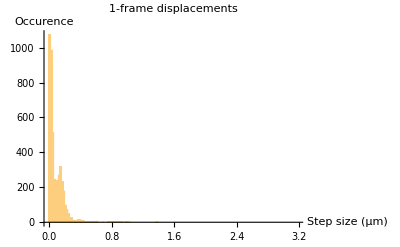

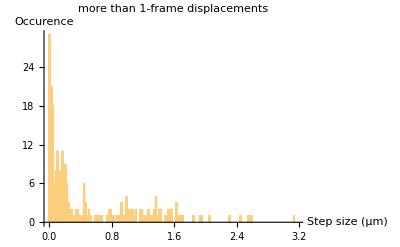

```mathematica
(* Prepare the result file for trajectory analysis *)

(* Removes the header in the data file: *)   
DataFileSmall=Drop[DataFile,Position[Transpose[DataFile][[2]],"Trajectory"][[2,1]]-1];   

(* Start positions of all trajectories: *)
Refer=Append[Flatten[Position[Transpose[DataFileSmall][[2]],"Trajectory"]],Length[DataFileSmall]+2];       

(* Create tables where each trajectory is a different element: MegaFile, SegmentedFile and SegmentedFileZero *)
MegaFile={};          (* Will contain particle trajectories (frame,x, y, i) *)
SegmentedFile={};        (* Will contain particle trajectories for plotting (x, y) *)
For [i=1, i ≤ntraj,i++,
TableGard={};
SegmentedTableGard={};
For [j=Refer[[i]]+2, j<Refer[[i+1]]-1, j++,    (* The +2 and -1 are for long file format *)
Gard=Take[DataFileSmall[[j]],{1,3}];   (* Take frame #, x, y *)
Gard[[3]]=ny-Gard[[3]];     (* Invert the image so it looks as in the movie *)
AppendTo[Gard,DataFileSmall[[j,5]]];    (* Take I *)
AppendTo[TableGard,Gard] ;    (* Frame #, x, y, I *)
AppendTo[SegmentedTableGard, Drop[Drop[Gard,1],-1]] (* x, y / used for plotting *)
];
AppendTo[MegaFile,TableGard];
AppendTo[SegmentedFile,SegmentedTableGard]
];
SegmentedFileZero=Table[SegmentedFile[[i,j]]-SegmentedFile[[i,1]],{i,ntraj},{j,Length[SegmentedFile[[i]]]}];  (* File with x, y, all starting at (0,0); only for visualization *)

(* Create a file with all displacements: *)
(* Displacements=Table[Sqrt[(SegmentedFile[[i,j+1,1]]-SegmentedFile[[i,j,1]])^2+(SegmentedFile[[i,j+1,2]]-SegmentedFile[[i,j,2]])^2]/(MegaFile[[i,j+1,1]]-MegaFile[[i,j,1]]),{i,ntraj},{j,Length[SegmentedFile[[i]]]-1}]; *)
Displacements=Table[Sqrt[(SegmentedFile[[i,j+1,1]]-SegmentedFile[[i,j,1]])^2+(SegmentedFile[[i,j+1,2]]-SegmentedFile[[i,j,2]])^2],{i,ntraj},{j,Length[SegmentedFile[[i]]]-1}];     (* Changed here to NOT normalize the displacement by time *)
(* Positions of displacements made over more than 1 frame *)
Jumps=Table[(MegaFile[[i,j+1,1]]-MegaFile[[i,j,1]])>1,{i,ntraj},{j,Length[SegmentedFile[[i]]]-1}];
(* Displacements made over more than 1 frame *)
BigDis=Table[Displacements[[i,Position[Jumps[[i]],True][[k]]]],{i,ntraj},{k,Length[Position[Jumps[[i]],True]]}];
(* Displacements made over exactly 1 frame *)
SmallDis=Table[Displacements[[i,Position[Jumps[[i]],False][[k]]]],{i,ntraj},{k,Length[Position[Jumps[[i]],False]]}];
(* Plot the 1-frame and >1-frame displacements *)
SmallDisF=Flatten[SmallDis]*psm;BigDisF=Flatten[BigDis]*psm;MaxDF=Max[Max[SmallDisF],Max[BigDisF]];
Histogram[Flatten[SmallDis]*psm,{0,MaxDF+0.05,0.02},PlotRange->Full,AxesLabel->{"Step size (μm)","Occurence"},PlotLabel->"1-frame displacements"]
Histogram[Flatten[BigDis]*psm,{0,MaxDF+0.05,0.02},PlotRange->Full,AxesLabel->{"Step size (μm)","Occurence"},PlotLabel->"more than 1-frame displacements"]

(* Creation of an info file for each trajectory containing: 1) number of detections (trajectory length in frames), 2) maximum 1-frame displacement (in pixels), 3) average intensity, 4) trajectory duration (in frames), 5) maximum displacement made when frames have been skipped (in pixels)  *)
PTrajInfo=Table[{Length[SegmentedFile[[i]]],If[Length[SmallDis[[i]]]>0,Max[SmallDis[[i]]],0],Mean[Transpose[MegaFile[[i]]][[4]]],MegaFile[[i,-1,1]]-MegaFile[[i,1,1]]+1,If[Length[BigDis[[i]]]>0,Max[BigDis[[i]]],0]},{i,ntraj}];
```

```mathematica
(* Show the output file so far *)
If[Output,Print[OutputFile1]];
```

VISUALIZATION AND VETTING OF TRAJECTORIES

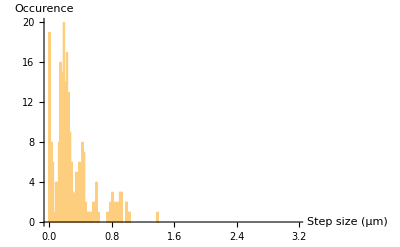

```mathematica
(* Histogram of max step sizes (per frame)*)
MDisplacement=Max[Transpose[PTrajInfo][[2]]]*psm;
Histogram[Transpose[PTrajInfo][[2]]*psm,{0,MaxDF+0.05,0.02},PlotRange->Full,AxesLabel->{"Step size (μm)","Occurence"}]
```

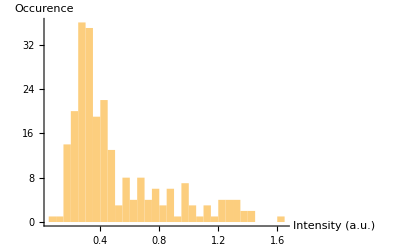

```mathematica
(* Histogram of average intensities *)
MInt=Mean[Transpose[PTrajInfo][[3]]];StdInt=StandardDeviation[Transpose[PTrajInfo][[3]]];
Show[Histogram[Transpose[PTrajInfo][[3]],{0,10,0.05}],PlotRange->Full,AxesLabel->{"Intensity (a.u.)","Occurence"}]
```

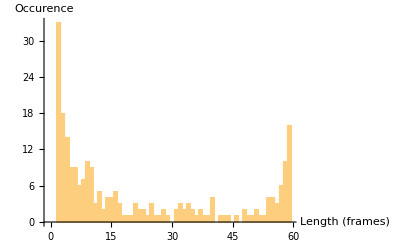

```mathematica
(* Histogram of trajectory lengths (how many frames are in the trajectory) *)
Show[Histogram[Transpose[PTrajInfo][[1]],{-0.5,nframes+0.5,1}],AxesLabel->{"Length (frames)","Occurence"}]
```

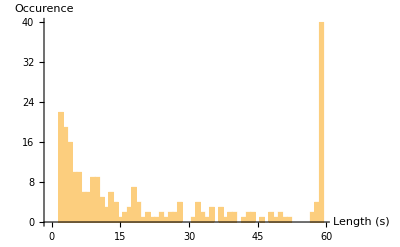

```mathematica
(* Histogram of trajectory durations (from first to last frame) *)
Show[Histogram[Transpose[PTrajInfo][[4]]*FrameTime,{-0.5,nframes+0.5,1}],AxesLabel->{"Length (s)","Occurence"}]
```

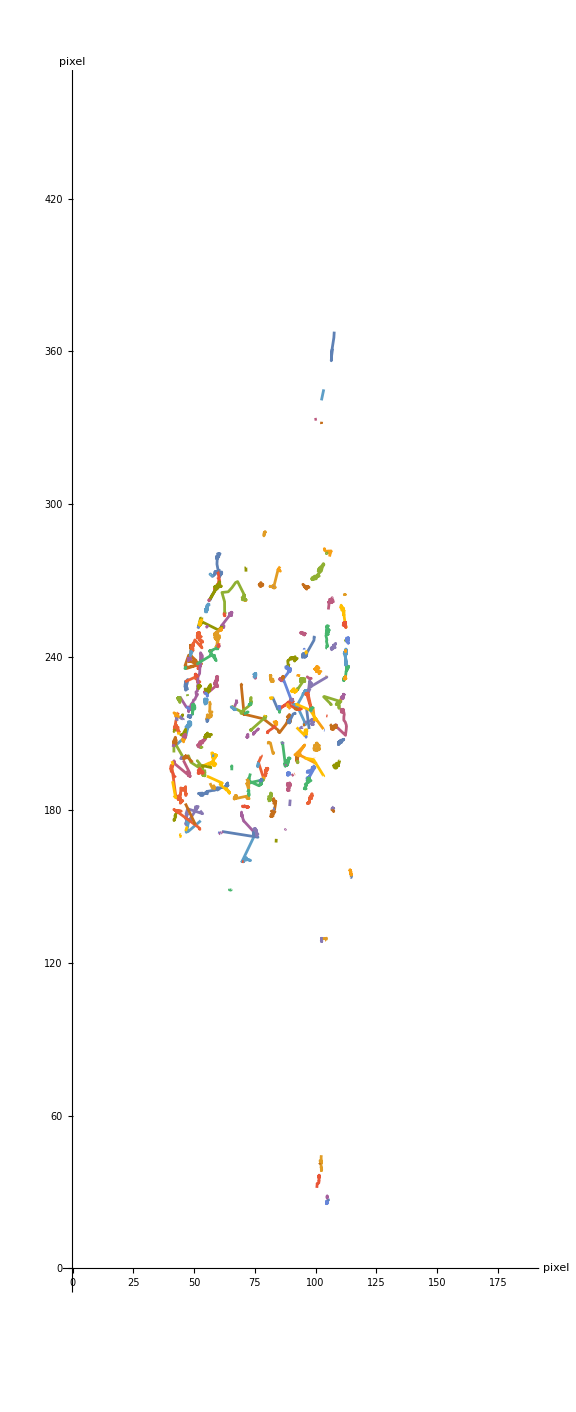

```mathematica
(* All detected trajectories (positions are in pixels) *)
ListPlot[SegmentedFile,PlotRange->{{0,nx},{0,ny}},AspectRatio->ny/nx,Joined->True,ImageSize->Large,AxesLabel->{"pixel","pixel"}]
```

```mathematica
(* Eliminate unwanted trajectories (short, dim, or with suspicious jumps) *)
(* Cut-off for number of detections in a trajectory *)
MinTrajLength = 8;     (* A minimal length of 6 is the cutoff applied by Mosaic *)
MaxVelocity=0.7;   (* 0.7 micron/s *)
MaxDisplacement=MaxVelocity/psm*FrameTime;  (* Maximum displacement allowed (in pxl) *)  
(* MaxDisplacement=2.7; *)
MaxBDisplacement =2.5;  (* 2.5 pixels *)
MinIntensity=MInt-StdInt;       (* Minimum average intensity allowed (calculated from mean and stdv) *)
MaxPercentLost=0.3;     (* Maximum percentage of frames where the particle is not detected *)
(* PTrajInfo: (1) Number of detections, (2) Maximum 1-frame displacement (pixel), (3) Average intensity, (4) Frame span, (5) Max displacement when a frame is missed (pixel) *)
(* Conditions for the trajectory to be retained: i) A minimum number of detections (MinTrajLength), ii) All 1-step displacement needs to be below a certain cut-off (step size for 1micron/s speed), iii) Average particle intensity is more than overall average particle intensity minus standard deviation, iv) number of missed frames is less than 30%  v) no displacement above a certain number of pixels *)
SantaList=Flatten[Position[PTrajInfo,{n_,m_,l_,k_,p_} /;n≥MinTrajLength && m≤MaxDisplacement && l≥MinIntensity && (k-n)/n≤MaxPercentLost  && p≤MaxBDisplacement ]];
ntrajClean=Length[SantaList];
Print["Number of detected trajectories: ",ntraj];
Print["Number of retained trajectories: ",ntrajClean];
If[Output,OutputFile2={{"Retained trajectories",ntrajClean},{"Minimum number of detections",MinTrajLength},{"Maximum allowed displacement in 1 frame (pxl)",MaxDisplacement},{"Maximum allowed displacement for missed frame(s) (pxl)",MaxBDisplacement},{"Minimum intensity",MinIntensity},{"Maximum fraction of missing detections",MaxPercentLost}}];
```

Null^2

Number of detected trajectories: 236

Number of retained trajectories: 90

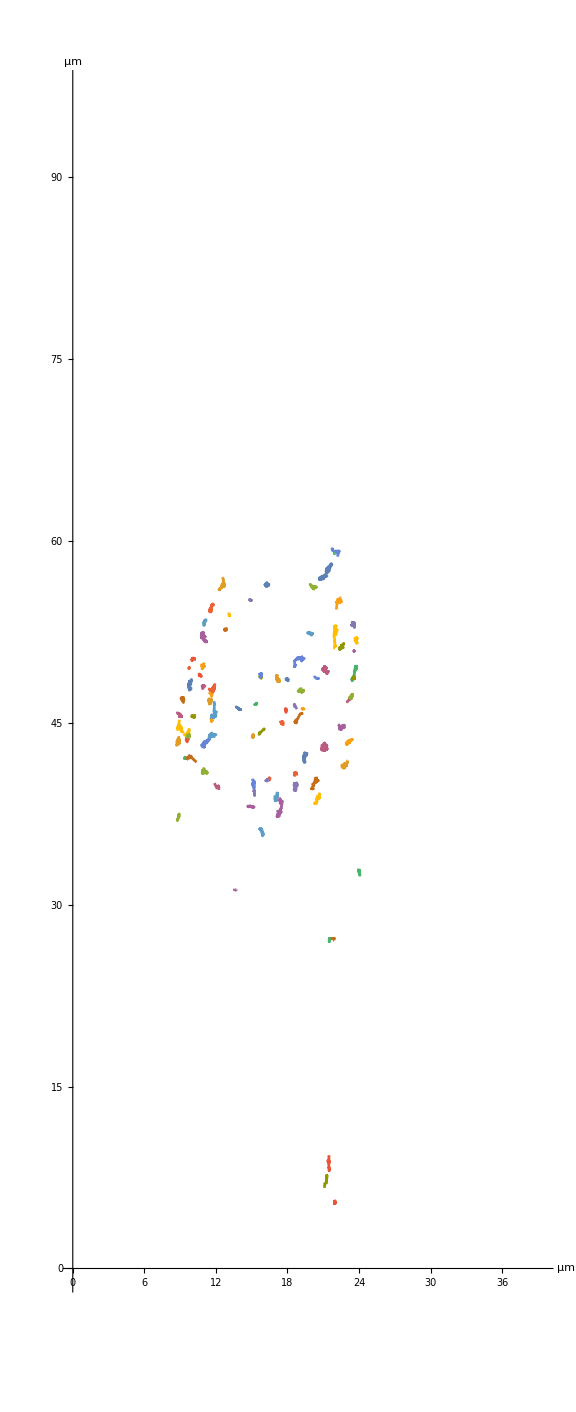

```mathematica
(**************** Clean trajectories (positions are in microns) ****************)
SegmentedFileClean=SegmentedFile[[SantaList]];
MegaFileClean=MegaFile[[SantaList]];
(* ListPlot[SegmentedFileClean*psm,PlotRange->{{0,nx*psm},{0,ny*psm}},AspectRatio->ny/nx,Joined->True,ImageSize->Large,AxesLabel->{"μm","μm"}] *)
(* ListPlot[SegmentedFileClean*psm,Joined->True,ImageSize->Large,AxesLabel->{"μm","μm"}] *)
xpos=0; ypos= 0; xpos0=0; ypos0=0;
size=nymax;
nymax=ny*psm;  nxmax=nx*psm;   (* Maximum possible and and y valuex in microns *)
Tra=ListPlot[SegmentedFileClean*psm,PlotRange->{{0,nxmax},{0,nymax}},AspectRatio->ny/nx,Joined->True,ImageSize->Large,AxesLabel->{"μm","μm"}(*,Epilog->Inset[SetAlphaChannel[Frame1,0.3],{xpos,ypos},{xpos0,ypos0},size]*)];
Tra=ListPlot[SegmentedFileClean*psm,PlotRange->{{0,nxmax},{0,nymax}},AspectRatio->ny/nx,Joined->True,ImageSize->Large,AxesLabel->{"μm","μm"}(*,Epilog->Inset[SetAlphaChannel[Frame1,0.3],{xpos,ypos},{xpos0,ypos0},size/1.4]*)];
Print[Tra];
```

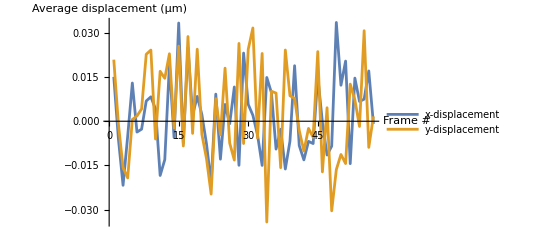

```mathematica
(* Calculating the average displacement (for all particles) at each frame, to see if there is a drift *)
MeanDis={};
For[k=1,k<nframes-1,k++,
GardDis={};
For[i=1,i<=ntrajClean,i++,
For[j=1,j<Length[MegaFileClean[[i]]],j++,
If[MegaFileClean[[i,j,1]]==k && MegaFileClean[[i,j+1,1]]==k+1,AppendTo[GardDis,{k,MegaFileClean[[i,j+1,2]]-MegaFileClean[[i,j,2]],MegaFileClean[[i,j+1,3]]-MegaFileClean[[i,j,3]]}]]
]
]
AppendTo[MeanDis,Mean[GardDis]];
];
ListPlot[{Transpose[{Transpose[MeanDis][[1]],Transpose[MeanDis][[2]]*psm}],Transpose[{Transpose[MeanDis][[1]],Transpose[MeanDis][[3]]*psm}]},Joined->True,PlotLegends->{"x-displacement","y-displacement"},AxesLabel->{"Frame #","Average displacement (μm)" }]
```

```mathematica
(* Show the output file so far *)
If[Output,Print[OutputFile2]];
```

DISTRIBUTION OF DISPLACEMENTS

```mathematica
(* Generation of the distribution of 1-step displacements for all trajectories *)

n=1;    (* Consider 1-step displacements first *)

PlotDis=Table[{},{i,ntrajClean}];      (* List of displacements (pxl) for each clean trajectory *)
PlotVelocities=Table[{},{i,ntrajClean}];    (* List of all velocities (micron/s) for each trajectory *)
TrajInfo=Table[{},{i,ntrajClean}];     (* List of trajectory lengths, average, min & max displacement *)

For [i=1, i ≤ntrajClean,i++,
Trajec=MegaFileClean[[i]];
If[Length[Trajec]>n,
For [j=1, j<Length[Trajec]+1-n, j++,
If[Trajec[[j+n,1]]==Trajec[[j,1]]+n,
Disx=Trajec[[j+n,2]]-Trajec[[j,2]];
Disy=Trajec[[j+n,3]]-Trajec[[j,3]];
Dis=Sqrt[Disx^2+Disy^2];
If[Dis != 0,       (* remove eventual mysterious cases of 0 displacement *)
AppendTo[PlotDis[[i]],{Dis,Disx,Disy}];
AppendTo[PlotVelocities[[i]],{Trajec[[j,1]],Disx*psm/(FrameTime*n),Disy*psm/(FrameTime*n)}]
]
];
],
AppendTo[PlotDis[[i]],{{},{},{}}];
AppendTo[PlotVelocities[[i]],{{},{},{}}];
];
TrajInfo[[i]]={SantaList[[i]],Length[Trajec],Mean[Transpose[PlotDis[[i]]][[1]]],Min[Transpose[PlotDis[[i]]][[1]]],Max[Transpose[PlotDis[[i]]][[1]]]};
];
```

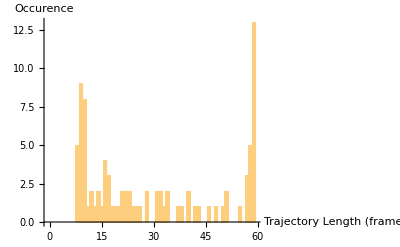

```mathematica
(* Lengths of the considered trajectories *)
Histogram[Transpose[TrajInfo][[2]],{-0.5,nframes+0.5,1},AxesLabel->{"Trajectory Length (frames)","Occurence"}]
```

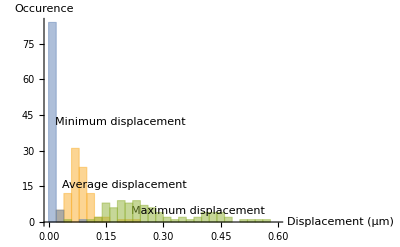

```mathematica
(* Average, min and max 1-step displacements for the considered trajectories *)
Histogram[{Labeled[DeleteCases[Transpose[TrajInfo][[3]]*psm,{}],"Average displacement",Left],Labeled[DeleteCases[Transpose[TrajInfo][[4]]*psm,{}],"Minimum displacement",Left],Labeled[DeleteCases[Transpose[TrajInfo][[5]]*psm,{}],"Maximum displacement",Right]},{0,Max[Transpose[TrajInfo][[5]]]*psm,0.02}, AxesLabel->{"Displacement (μm)","Occurence"}]
```

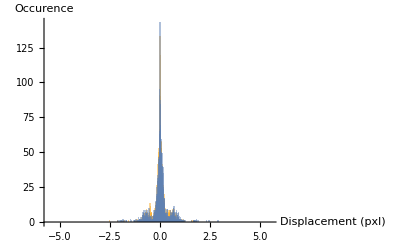

```mathematica
(* Distribution of displacement along x and y - all trajectories *)
Show[Histogram[{DeleteCases[Transpose[Flatten[PlotDis,1]][[2]],{}],DeleteCases[Transpose[Flatten[PlotDis,1]][[3]],{}]},{-Sqrt[n]*MDisplacement*4,Sqrt[n]*MDisplacement*4,0.01}],AxesLabel->{"Displacement (pxl)","Occurence"}]
```

{m→1.82562,s→0.0923147}

General::munfl: Exp[-3305.1] is too small to represent as a normalized machine number; precision may be lost.

{m→2.49009,s→0.0684907,f2→0.481271,s2→0.438519}

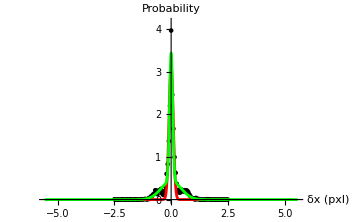

```mathematica
(********** Fit normalized DisDis-x with a Gaussian ********)
Fitfunction[m_,s_,f2_,s2_,pix_]:=(m/(2*Pi))*((1-f2)/s*ⅇ^(-pix^2/(2 s^2))+f2/s2*ⅇ^(-pix^2/(2 s2^2)) );
BinSize=0.05*n;
(* Plot distribution *)
ListDis=DeleteCases[Transpose[Flatten[PlotDis,1]][[2]],{}];
MM=Max[ListDis];mm=Min[ListDis];MMmm=Round[Max[MM,-mm],BinSize];
Bins=Table[i,{i,-MMmm,MMmm,BinSize}];
BinCs=BinCounts[ListDis,{-MMmm-BinSize/2,MMmm+BinSize/2,BinSize}];
binneddistrib0=Transpose[{Bins,BinCs}];binneddistrib=Table[{binneddistrib0[[i,1]],binneddistrib0[[i,2]]/Length[ListDis]/BinSize},{i,Length[binneddistrib0]}];
DataPx=ListPlot[binneddistrib,PlotRange->{{-Sqrt[n]*MDisplacement*4,Sqrt[n]*MDisplacement*4},{0,Max[Transpose[binneddistrib][[2]]]+0.2}},PlotStyle->Black,ImageSize->Medium,AxesLabel->{"δx (pxl)","Probability"}];
(* 1-component fit *)
bestfitx=FindFit[binneddistrib,{Fitfunction[m,s,0,1,pix]},{{m,Max[Transpose[binneddistrib][[2]]]},{s,0.2}},pix];
FitPx=Plot[Fitfunction[m,s,0,1,pix]/.bestfitx,{pix,-MDisplacement,MDisplacement},PlotRange->{0,Max[Transpose[binneddistrib][[2]]]},PlotStyle->Red];
Print[bestfitx];
(* 2-component fit *)
bestfit2x=FindFit[binneddistrib,{Fitfunction[m,s,f2,s2,pix]},{{m,Max[Transpose[binneddistrib][[2]]]},{s,0.2},{f2,0.2},{s2,0.6}},pix];
FitP2x=Plot[Fitfunction[m,s,f2,s2,pix]/.bestfit2x,{pix,-Sqrt[n]*MDisplacement*4,Sqrt[n]*MDisplacement*4},PlotRange->{0,Max[Transpose[binneddistrib][[2]]]},PlotStyle->Green];
Print[bestfit2x];
Show[DataPx,FitPx,FitP2x]
```

General::munfl: Exp[-1577.94] is too small to represent as a normalized machine number; precision may be lost.

{m→1.76902,s→0.0991241}

General::munfl: Exp[-2635.07] is too small to represent as a normalized machine number; precision may be lost.

{m→2.4969,s→0.0767058,f2→0.470011,s2→0.577276}

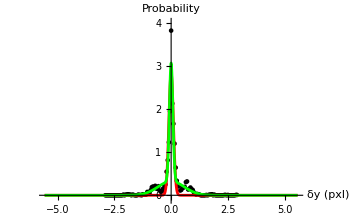

```mathematica
(********** Fit DisDis-y with a Gaussian ********)
Fitfunction[m_,s_,f2_,s2_,pix_]:=(m/(2*Pi))*((1-f2)/s*ⅇ^(-pix^2/(2 s^2))+f2/s2*ⅇ^(-pix^2/(2 s2^2)) );
BinSize=0.05*n;
(* Plot distribution *)
ListDis=DeleteCases[Transpose[Flatten[PlotDis,1]][[3]],{}];
MM=Max[ListDis];mm=Min[ListDis];MMmm=Round[Max[MM,-mm],BinSize];
Bins=Table[i,{i,-MMmm,MMmm,BinSize}];
BinCs=BinCounts[ListDis,{-MMmm-BinSize/2,MMmm+BinSize/2,BinSize}];
binneddistrib0=Transpose[{Bins,BinCs}];
binneddistrib=Table[{binneddistrib0[[i,1]],binneddistrib0[[i,2]]/Length[ListDis]/BinSize},{i,Length[binneddistrib0]}];
DataPy=ListPlot[binneddistrib,PlotRange->{{-Sqrt[n]*MDisplacement*4,Sqrt[n]*MDisplacement*4},{-0.1,Max[Transpose[binneddistrib][[2]]]+0.2}},PlotStyle->Black,ImageSize->Medium,AxesLabel->{"δy (pxl)","Probability"}];
(* 1-component fit *)
bestfity=FindFit[binneddistrib,{Fitfunction[m,s,0,1,pix]},{{m,Max[Transpose[binneddistrib][[2]]]},{s,0.1}},pix];
FitPy=Plot[Fitfunction[m,s,0,1,pix]/.bestfity,{pix,-MDisplacement*4,MDisplacement*4},PlotRange->{0,Max[Transpose[binneddistrib][[2]]]},PlotStyle->Red];
Print[bestfity];
(* 2-component fit *)
bestfit2y=FindFit[binneddistrib,{Fitfunction[m,s,f2,s2,pix]},{{m,Max[Transpose[binneddistrib][[2]]]},{s,0.1},{f2,0.2},{s2,0.5}},pix];
FitP2y=Plot[Fitfunction[m,s,f2,s2,pix]/.bestfit2y,{pix,-Sqrt[n]*MDisplacement*4,Sqrt[n]*MDisplacement*4},PlotRange->{0,Max[Transpose[binneddistrib][[2]]]},PlotStyle->Green];
Print[bestfit2y];
Show[DataPy,FitPy,FitP2y]
```

```mathematica
(* Create and fit the distribution of step size for the retained trajectories *)
```

```mathematica
(* Fitting functions *)
FitBrownian[s_,r_]:=(1/s^2 )*r*ⅇ^(-r^2/(2 s^2));   (* Rayleigh's distribution *)
FitDirected[rD_,sD_,r_]:=Exp[-(r-rD)^2/2/sD^2]*√(2/π)/sD/(1+Erf[rD/sD/√2]);   (* Gaussian distribution *)
(* 1 diffusive component *)  
Fitfunction1[f1_,s1_,r_]:=f1*FitBrownian[s1,r];     
(* 2 diffusive components *) 
Fitfunction2[f1_,s1_,f2_,s2_,r_]:=f1*FitBrownian[s1,r]+f2*FitBrownian[s2,r] ;   
(* 3 diffusive components *)  Fitfunction3[f1_,s1_,f2_,s2_,f3_,s3_,r_]:=f1*FitBrownian[s1,r]+f2*FitBrownian[s2,r] +f3*FitBrownian[s3,r] ;
(* 1 diffusive and 1 directed components *)  Fitfunction4[f1_,s1_,fD1_,rD1_,sD1_,r_]:=f1*FitBrownian[s1,r]+fD1*FitDirected[rD1,sD1,r];
(* 2 diffusive and 1 directed components *)  Fitfunction5[f1_,s1_,f2_,s2_,fD1_,rD1_,sD1_,r_]:=f1*FitBrownian[s1,r]+f2*FitBrownian[s2,r]+fD1*FitDirected[rD1,sD1,r];
```

{f1→0.533011,s1→0.0216702}

{f1→0.448064,s1→0.0188899,f2→0.498282,s2→0.102912}

{f1→0.448064,s1→0.0188899,f2→0.2493,s2→0.102882,f3→0.248982,s3→0.102943}

{f1→0.31802,s1→0.0181604,fD1→0.679462,rD1→0.0181605,sD1→0.121703}

{f1→0.0729225,s1→0.00394757,f2→0.455969,s2→0.0216654,fD1→0.444539,rD1→0.126757,sD1→0.0623697}

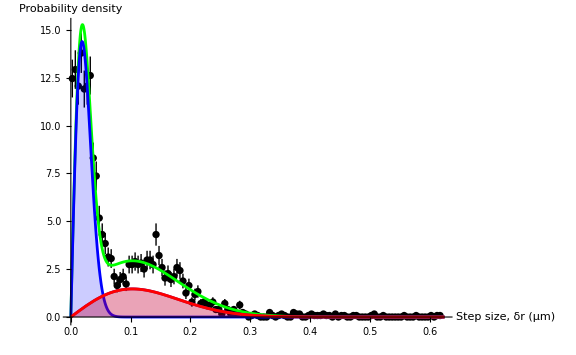

Precision of particle localization: σ = 18.8899 nm

Diffusion coefficient of Brownian particles: D = 5.29237 x 10^(-3) µm^2/s

Diffusion coefficient of Brownian particles: D = 5.2986 x 10^(-3) µm^2/s

Typical speed of directed particles: v = rD1µm/s

```mathematica
(* Calculate distribution of 1-frame steps for clean trajectories in microns *)
BinSize=0.005*Sqrt[n];
ListDisM=DeleteCases[Transpose[Flatten[PlotDis,1]][[1]],{}]*psm;
MM=Max[ListDisM];mm=Min[ListDisM];MMmm=Round[Max[MM,-mm],BinSize];
Bins=Table[i,{i,BinSize/2,MMmm+BinSize/2,BinSize}];
BinCs=BinCounts[ListDisM,{0,MMmm+BinSize,BinSize}];
binneddistrib01=Transpose[{Bins,BinCs}];   (* Distribution *)
binneddistrib1=Table[{binneddistrib01[[i,1]],binneddistrib01[[i,2]]/Length[ListDisM]/BinSize},{i,Length[binneddistrib01]}];  (* Normalized *)
binneddistriberr1=Table[{binneddistrib01[[i,1]],Around[binneddistrib01[[i,2]]/Length[ListDisM]/BinSize,Sqrt[binneddistrib01[[i,2]]]/Length[ListDisM]/BinSize]},{i,Length[binneddistrib01]}];     (* With error bars *)
(* Plot distribution *)
Maxr=MMmm+2*BinSize;MaxY=Max[Transpose[binneddistrib1][[2]]]+1.5;
DataP=ListPlot[binneddistriberr1,PlotRange->{{0,Maxr},{-0.1,MaxY}},PlotStyle->Black,AxesLabel->{"Step size, δr (μm)","Probability density"},ImageSize->Large]; 
(* Fit distribution *)
(* 1 diffusive component *)
bestfitr1=FindFit[binneddistrib1,{Fitfunction1[f1,s1,r],f1>0&&s1>0},{{f1,0.6},{s1,0.03}},r];
Fitr1=Plot[Fitfunction1[f1,s1,r]/.bestfitr1,{r,0,Maxr},PlotRange->{{0,Maxr},{0,MaxY}},PlotStyle->Red];
Print[bestfitr1];
(* 2 diffusive components *)
bestfitr2=FindFit[binneddistrib1,{Fitfunction2[f1,s1,f2,s2,r],f1>0&&s1>0&&f2>0&& s2>s1},{{f1,f1/.bestfitr1},{s1,s1/.bestfitr1},{f2,1-f1/.bestfitr1},{s2,0.15}},r];
Fitr2=Plot[Fitfunction2[f1,s1,f2,s2,r]/.bestfitr2,{r,0,Maxr},PlotRange->{{0,Maxr},{0,MaxY}},PlotStyle->Blue];
Print[bestfitr2];
(* 3 diffusive components *)
bestfitr3=FindFit[binneddistrib1,{Fitfunction3[f1,s1,f2,s2,f3,s3,r],f1>0&&s1>0&&s1<0.04&&f2>0&& s2>s1&& f3>0 && s3>s2},{{f1,0.5},{s1,s1/.bestfitr2},{f2,0.5},{s2,s2/.bestfitr2},{f3,0.2},{s3,0.15}},r];
Fitr3=Plot[Fitfunction3[f1,s1,f2,s2,f3,s3,r]/.bestfitr3,{r,0,Maxr},PlotRange->{{0,Maxr},{0,MaxY}},PlotStyle->Green];
Print[bestfitr3];
(* 1 diffusive and 1 directed component *)   
bestfitr4=FindFit[binneddistrib1,{Fitfunction4[f1,s1,fD1,rD1,sD1,r],f1>0&&s1>0&&fD1>0&& rD1>s1&&sD1>0},{{f1,0.5},{s1,s1/.bestfitr2},{fD1,0.5},{rD1,s2/.bestfitr2},{sD1,0.2}},r];
Fitr4=Plot[Fitfunction4[f1,s1,fD1,rD1,sD1,r]/.bestfitr4,{r,0,Maxr},PlotRange->{{0,Maxr},{0,MaxY}},PlotStyle->Orange];
Print[bestfitr4];
(* 1 diffusive and 1 directed component *)   
bestfitr5=FindFit[binneddistrib1,{Fitfunction5[f1,s1,f2,s2,fD1,rD1,sD1,r],f1>0&&s1>0&&f2>0&&s2>s1&&fD1>0&&fD1<1&& rD1>s2&&rD1<Maxr&&sD1>0&&sD1<Maxr},{{f1,0.3},{s1,s1/.bestfitr3},{f2,0.5},{s2,s2/.bestfitr3},{fD1,0.2},{rD1,0.35},{sD1,0.08}},r];
Fitr5=Plot[Fitfunction5[f1,s1,f2,s2,fD1,rD1,sD1,r]/.bestfitr5,{r,0,Maxr},PlotRange->{{0,Maxr},{0,MaxY}},PlotStyle->Purple];
Print[bestfitr5];

(* Chose the best model *)
Model=3;   
CurveFits={Fitr1,Fitr2,Fitr3,Fitr4,Fitr5};
Fits={bestfitr1,bestfitr2,bestfitr3,bestfitr4,bestfitr5};
FitFF1=Plot[f1*FitBrownian[s1,r]/.Fits[[Model]],{r,0,Maxr},PlotRange->All,PlotStyle->{Blue},Filling->Bottom];
FitFF2=Plot[f2*FitBrownian[s2,r]/.Fits[[Model]],{r,0,Maxr},PlotRange->All,PlotStyle->{Purple},Filling->Bottom];
FitFF3=Plot[f3*FitBrownian[s3,r]/.Fits[[Model]],{r,0,Maxr},PlotRange->All,PlotStyle->{Red},Filling->Bottom];
FitFF4=Plot[fD1*FitDirected[rD1,sD1,r]/.Fits[[Model]],{r,0,Maxr},PlotRange->All,PlotStyle->{Red},Filling->Bottom];
If[Output,OutputFile3=OutRes={{"Fraction of immobile steps",f1},{"Average length of immobile steps",s1},{"Fraction of Brownian steps",f2},{"Estimated diffusion coefficient from average Brownian step length (µm^2/s)", s2^2/2/FrameTime},{"Fraction of fast Brownian steps",f3},{"Estimated fast diffusion coefficient from average fast Brownian step length (µm^2/s)",s3^2/2/FrameTime},{"Fraction of active steps",fD1},{"Estimated velocity from average active steps length (µm/s)",rD1/FrameTime},{"Standard deviation of active steps length",sD1}}/.Fits[[Model]]];
Show[DataP,CurveFits[[Model]],FitFF1,FitFF2,FitFF3,FitFF4]
Print["Precision of particle localization: σ = ",s1*1000/.Fits[[Model]]," nm"];
Print["Diffusion coefficient of Brownian particles: D = ",s2^2/2/FrameTime*1000/.Fits[[Model]]," x 10^(-3) µm^2/s"];
Print["Diffusion coefficient of Brownian particles: D = ",s3^2/2/FrameTime*1000/.Fits[[Model]]," x 10^(-3) µm^2/s"];
Print["Typical speed of directed particles: v = ", rD1/FrameTime/.Fits[[Model]],"µm/s"];
```

```mathematica
Show[DataP,CurveFits[[Model]],FitFF1,FitFF2,FitFF3,FitFF4]
```

-Graphics-

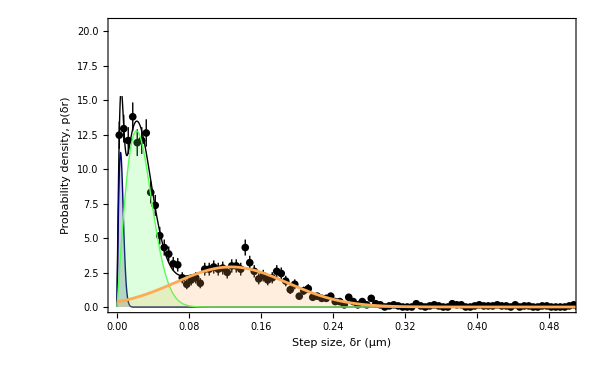

```mathematica
(* Publication-quality figure *)
DataP=ListPlot[binneddistriberr1,PlotRange->{{0,0.5},{0,20.5}},PlotStyle->Black,Frame->True,FrameStyle->{{Directive[20,Black,Thickness[0.003]],Directive[20,White,Thickness[0.003]]},{Directive[20,Black,Thickness[0.003]],Directive[20,White,Thickness[0.003]]}},FrameLabel->{"Step size, δr (μm)","Probability density, p(δr)"},ImageSize->600];
Fitr2=Plot[Fitfunction2[f1,s1,f2,s2,r]/.bestfitr2,{r,0,Maxr},PlotRange->{{0,Maxr},{0,MaxY}},PlotStyle->{Black,Thick}];
Fitr5=Plot[Fitfunction5[f1,s1,f2,s2,fD1,rD1,sD1,r]/.bestfitr5,{r,0,Maxr},PlotRange->{{0,Maxr},{0,MaxY}},PlotStyle->{Black,Thick}];
FitFF1=Plot[f1*FitBrownian[s1,r]/.bestfitr5,{r,0,Maxr},PlotRange->All,PlotStyle->{color1,Thin},Filling->Bottom];
FitFF2=Plot[f2*FitBrownian[s2,r]/.bestfitr5,{r,0,Maxr},PlotRange->All,PlotStyle->{color2,Thin},Filling->Bottom];
FitFF4=Plot[fD1*FitDirected[rD1,sD1,r]/.bestfitr5,{r,0,Maxr},PlotRange->All,PlotStyle->{color3},Filling->Bottom];
Show[DataP,Fitr5,FitFF1,FitFF2,FitFF4]
```

Conclusion: The distribution of displacements can be explained assuming that we have three different populations of particles, which could be: 1) Completely immobilized particles that seem to move from frame to frame only because of detection noise; 2) Slowly diffusing particles; and 3) Active particles undergoing fast directed motion.

The limit step size between immobile and mobile particle is: 0.0566697 µm

The limit step size between diffusing and directed particles is: 0.308647 µm

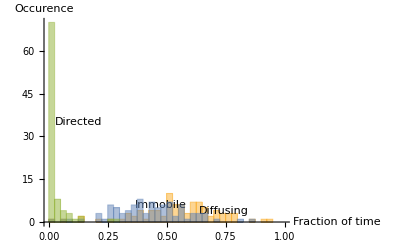

```mathematica
(* We decide here how to distinguish between populations, by defining bound1 that separates immobile from diffusive motion, and bound 2, that separates diffusive from directed motion *)
(* Fraction of time spent immobile, diffusing, or in active motion *)
If[Model==1 ||Model==4,bound1 = 0;bound2=3*s1/.Fits[[Model]]]; 
If[Model==2||Model==3||Model==5,bound1 = 3*s1/.Fits[[Model]];bound2=3*s2/.Fits[[Model]]];  
(* Division between immobile and diffusing is 2 times the mean immobile step size, and that between mobile and directed is 3 times the mean diffusive step size *)
Print["The limit step size between immobile and mobile particle is: ", bound1," µm"];
Print["The limit step size between diffusing and directed particles is: ", bound2," µm"];

(* Calculate, for each trajectory, the fraction of steps spent immobile, diffusing or directed *)
ProStep=Table[{},{i,ntrajClean}];TernaryStep=Table[{},{i,ntrajClean}];
For [i=1, i≤ntrajClean,i++,
Listi=Transpose[PlotDis[[i]]][[1]];
n0=Length[Listi];
n1=Length[Cases[Listi,n_ /; n<bound1/psm]];   (* Steps shorter than 3 times the noise stdv are considered to belong to immobilized particles *)
n3=Length[Cases[Listi,n_ /; n>bound2/psm]];
(* Steps longer than 3 times the diffusion peak stdv are considered to belong to active particles *)
n2=n0-n1-n3;
(* Other steps are considered to belong to diffusing particles *)
ProStep[[i]]={n0,n1,n2,n3,N[n1/n0],N[n2/n0],N[n3/n0]};
TernaryStep[[i]]={N[n1/n0],N[n2/n0],N[n3/n0]};
AppendTo[TrajInfo[[i]],ProStep[[i]]];
TrajInfo[[i]]=Flatten[TrajInfo[[i]]]
];
(* TernaryListPlot[TernaryStep]; *)  (* This will work when I upgrade to version 13.1 *)
Histogram[{Labeled[Transpose[ProStep][[5]],"Immobile",Top],Labeled[Transpose[ProStep][[6]],"Diffusing",Right],Labeled[Transpose[ProStep][[7]],"Directed",Left]},{0,1,0.025},AxesLabel->{"Fraction of time","Occurence"}]
(* Yellow: Immobile, Blue: Diffusing, Green: Directed *)

If[Output,OutputFile3=Join[OutputFile3,{{"Bound 1 (µm)",bound1},{"Bound 2 (µm)",bound2}}]];
```

```mathematica
(* Show the output file so far *)
If[Output,Print[OutputFile3]];
```

Conclusion: Most particles show a diffusive motion for most of their trajectories, with steps where they seem completely immobilized (between 10 to 80% of the time). Note that even for particles diffusing all of the time, we would expect a fraction of the steps to be below the threshold of what can be resolved (appearing immobile).  A few particles also demonstrate active linear motion for about 30% of the time.

EVOLUTION OF THE DISTRIBUTION OF DISPLACEMENTS

```mathematica
(* Generation of the distribution of n-step displacements for all trajectories *)

nmax=20;

PlotDisN=Table[{},{i,ntrajClean},{n,nmax}];      (* List of displacements (pxl) for each trajectory *)
binneddistrib={};                                            (*  List that will contain all the distributions of displacement  *)
bestfit2xy={};                                  (* List that will contain the result of the distribution fits *)
DiffCoeff={};                            (* List will contain the predicted values of the diffusion coefficients in μm2/s *)

For[n=1,n≤nmax,n=n+1,

(* Calculate displacements for a given time interval for all trajectories *)
For[i=1, i ≤ntrajClean,i++,
Trajec=MegaFileClean[[i]];
If[Length[Trajec]>n,
For [j=1, j<Length[Trajec]+1-n, j++,
If[Trajec[[j+n,1]]==Trajec[[j,1]]+n,
Disx=Trajec[[j+n,2]]-Trajec[[j,2]];
Disy=Trajec[[j+n,3]]-Trajec[[j,3]];
Dis=Sqrt[Disx^2+Disy^2];
If[Dis != 0,AppendTo[PlotDisN[[i,n]],{Dis,Disx,Disy}];]
];
],
AppendTo[PlotDisN[[i,n]],{{},{},{}}];
];
];

(* Save and plot the distribution of displacement *)
BinSize=0.04*Sqrt[n];
ListDis=DeleteCases[Transpose[Flatten[Transpose[PlotDisN][[n]],1]][[1]],{}]; 
MM=Max[ListDis];mm=Min[ListDis];MMmm=Round[Max[MM,-mm],BinSize];
Bins=Table[i,{i,BinSize/2,MMmm+BinSize/2,BinSize}];
BinCs=BinCounts[ListDis,{0,MMmm+BinSize,BinSize}];
binneddistrib0=Transpose[{Bins,BinCs}];binneddistrib=AppendTo[binneddistrib,Table[{binneddistrib0[[i,1]],binneddistrib0[[i,2]]/Length[ListDis]/BinSize},{i,Length[binneddistrib0]}]];

(* Fit the distribution of displacement Dis-Dis-r *)
Fitfunction[m_,s_,f2_,s2_,f3_,s3_,pix_]:=m*((1-f2-f3)*pix*ⅇ^(-pix^2/(2 s^2))/s^2+f2*pix*ⅇ^(-pix^2/(2 s2^2))/s2^2+f3*pix*ⅇ^(-pix^2/(2 s3^2)) /s3^2);
bestfit2xy=AppendTo[bestfit2xy,FindFit[binneddistrib[[n]],{Fitfunction[m,s,f2,s2,f3,s3,pix],s>0.1},{{m,0.95},{s,0.27},{f2,0.6},{s2,0.6},{f3,0.14},{s3,2.27}},pix]];
DiffCoeff=AppendTo[DiffCoeff,{FrameTime*n,(s*psm)^2/2/(FrameTime*n),(s2*psm)^2/2/(FrameTime*n),(s3*psm)^2/2/(FrameTime*n)}/.bestfit2xy[[n]]];

];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{m→3.091,s→0.1,f2→0.153631,s2→0.517146,f3→0.691465,s3→66.0802}

{m→0.949853,s→0.664028,f2→84.3944,s2→0.66558,f3→0.258202,s3→1.93338}

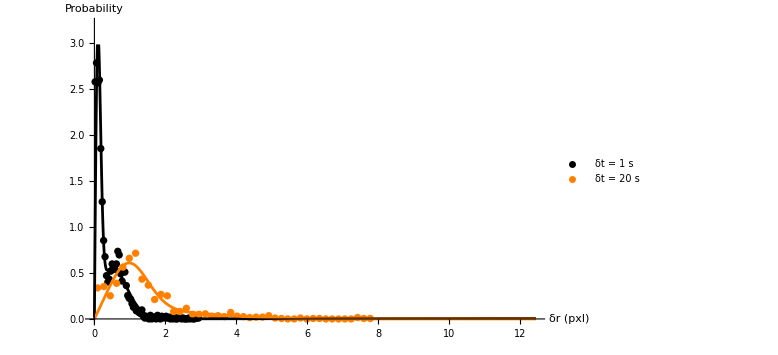

```mathematica
(* Plotting distribution of displacement and fits *)

DataPr=ListPlot[{binneddistrib[[1]],binneddistrib[[nmax]]},PlotRange->{{0,Sqrt[nmax]*MDisplacement*2},{0,Min[3.2,Max[Transpose[binneddistrib[[1]]][[2]]]+0.5]}},Joined->False,ImageSize->Large,AxesLabel->{"δr (pxl)","Probability"},PlotStyle->{Black,Orange},PlotLegends->{"δt = " <>ToString[FrameTime]<>" s","δt = " <>ToString[FrameTime*nmax]<>" s"}];

FitPr2=Plot[{Fitfunction[m,s,f2,s2,f3,s3,pix]/.bestfit2xy[[1]],Fitfunction[m,s,f2,s2,f3,s3,pix]/.bestfit2xy[[nmax]]},{pix,-0,Sqrt[nmax]*MDisplacement*2},PlotRange->{{0,Sqrt[nmax]*MDisplacement*2},{0,Min[3.2,Max[Transpose[binneddistrib[[1]]][[2]]]+0.2]}},PlotStyle->{Black,Orange}];
Print[bestfit2xy[[1]]];Print[bestfit2xy[[nmax]]];
Show[DataPr,FitPr2]
```

{f1→0.467074,s1→0.0192399,f2→0.378017,s2→0.10386,f3→0.117245,s3→0.10386}

{f1→0.062589,s1→0.025875,f2→0.821581,s2→0.194635,f3→0.133778,s3→0.565878}

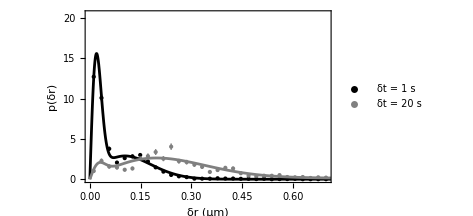

```mathematica
(* Generate the 20th disdis *)
nfirst=1;nlast=20;
BinSize=0.005*Sqrt[n];

ListDisF=DeleteCases[Transpose[Flatten[Transpose[PlotDisN][[nfirst]],1]][[1]],{}]*psm;  (* needs to be run 2x *)
ListDisL=DeleteCases[Transpose[Flatten[Transpose[PlotDisN][[nlast]],1]][[1]],{}]*psm;
MM=Max[Join[ListDisF,ListDisL]]; mm=Min[Join[ListDisF,ListDisL]]; MMmm=Round[Max[MM,-mm],BinSize];
Bins=Table[i,{i,BinSize/2,MMmm+BinSize/2,BinSize}];    (* bins *)
BinCF=BinCounts[ListDisF,{0,MMmm+BinSize,BinSize}]; BinCL=BinCounts[ListDisL,{0,MMmm+BinSize,BinSize}];    (* counts  *)
binneddistrib0F=Transpose[{Bins,BinCF}]; binneddistrib0L=Transpose[{Bins,BinCL}];   (* Distributions *)
binneddistribF=Table[{binneddistrib0F[[i,1]],binneddistrib0F[[i,2]]/Length[ListDisF]/BinSize},{i,Length[binneddistrib0F]}];  
binneddistribL=Table[{binneddistrib0L[[i,1]],binneddistrib0L[[i,2]]/Length[ListDisL]/BinSize},{i,Length[binneddistrib0L]}];  
binneddistriberrF=Table[{binneddistrib0F[[i,1]],Around[binneddistrib0F[[i,2]]/Length[ListDisF]/BinSize,Sqrt[binneddistrib0F[[i,2]]]/Length[ListDisF]/BinSize]},{i,Length[binneddistrib0F]}];      (* Distributions with error bars *)
binneddistriberrL=Table[{binneddistrib0L[[i,1]],Around[binneddistrib0L[[i,2]]/Length[ListDisL]/BinSize,Sqrt[binneddistrib0L[[i,2]]]/Length[ListDisL]/BinSize]},{i,Length[binneddistrib0L]}];

(* Fit with 3 diffusive components *)  Fitfunction3[f1_,s1_,f2_,s2_,f3_,s3_,r_]:=f1*FitBrownian[s1,r]+f2*FitBrownian[s2,r] +f3*FitBrownian[s3,r] ;
bestfitF=FindFit[binneddistribF,{Fitfunction3[f1,s1,f2,s2,f3,s3,r],s1>0.01},{{f1,0.55},{s1,0.02},{f2,0.35},{s2,0.1},{f3,0.1},{s3,0.2}},r];
bestfitL=FindFit[binneddistribL,{Fitfunction3[f1,s1,f2,s2,f3,s3,r],s1>0.01},{{f1,0.1},{s1,0.036},{f2,0.75},{s2,0.165},{f3,0.1},{s3,0.5}},r];

(* Publication quality figure *)
nfs=14;
DataPs=ListPlot[{binneddistriberrF,binneddistriberrL},PlotRange->{{0,0.7},{0,20.5}},Joined->False,ImageSize->350,PlotStyle->{{Black,PointSize->0.015},{Gray,PointSize->0.015}},Frame->True,FrameStyle->{{Directive[nfs,Black,Thickness[0.003]],Directive[nfs,White,Thickness[0.003]]},{Directive[nfs,Black,Thickness[0.003]],Directive[nfs,White,Thickness[0.003]]}},FrameLabel->{"δr (μm)","p(δr)"},PlotLegends->{"δt = " <>ToString[FrameTime*nfirst]<>" s","δt = " <>ToString[FrameTime*nlast]<>" s"}];

FitPr2=Plot[{Fitfunction3[f1,s1,f2,s2,f3,s3,r]/.bestfitF,Fitfunction3[f1,s1,f2,s2,f3,s3,r]/.bestfitL},{r,0,1},PlotRange->{{0,1},{0,18.3}},PlotStyle->{Black,Gray}];Print[bestfitF];Print[bestfitL];
Show[DataPs,FitPr2]
```

The precision of the localization is: 48.6001 nm

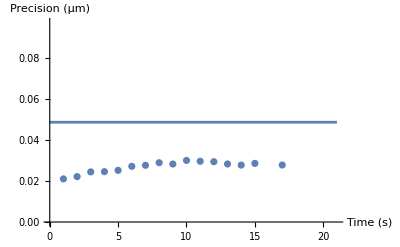

```mathematica
(*  Precision of particle localization, assuming the first population is that that remains completely immobile for at least nmax frames *)
Precise=Table[{FrameTime*n,s*psm/.bestfit2xy[[n]]},{n,nmax}];
FitF[a_,t_]:=a+0*t;
BestF=FindFit[Precise,FitF[a,t],{a},t];
PlotD=ListPlot[Precise,PlotRange->{{0,nmax*FrameTime+1},{0,2*a/.BestF}},AxesLabel->{"Time (s)", "Precision (µm)"}];
PlotF=Plot[FitF[a,t]/.BestF,{t,0,nmax*FrameTime+1}];
Precisely=a*1000/.BestF; Print["The precision of the localization is: ",Precisely," nm"]
Print[Show[PlotD,PlotF]];
```

{a→0.0118425,b→0.246624}

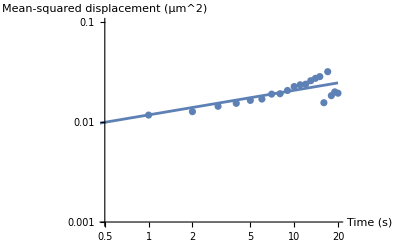

```mathematica
(*  Slow diffusion  *)
DiffS=Table[{FrameTime*n,s2^2*psm^2/.bestfit2xy[[n]]},{n,nmax}];
FitF[a_,b_,t_]:=a*t^b;
BestF=FindFit[DiffS,FitF[a,b,t],{a,b},t];
PlotD=ListLogLogPlot[DiffS,PlotRange->{{FrameTime/2,nmax*FrameTime},{0.001,0.1}},AxesLabel->{"Time (s)", "Mean-squared displacement (µm^2)"}];
PlotF=LogLogPlot[FitF[a,b,t]/.BestF,{t,0,nmax*FrameTime}];
Print[BestF];
Print[Show[PlotD,PlotF]];
```

The size of the cages is: 141.276 nm

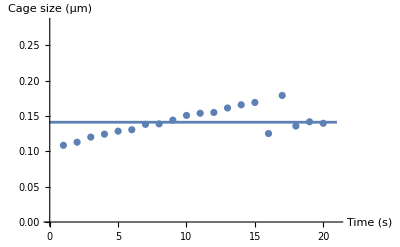

```mathematica
(*  Size of the cage if we assume the second term is caged particles *)
Precise2=Table[{FrameTime*n,s2*psm/.bestfit2xy[[n]]},{n,nmax}];
FitF[a_,t_]:=a+0*t;
BestF2=FindFit[Precise2,FitF[a,t],{a},t];
PlotD2=ListPlot[Precise2,PlotRange->{{0,nmax*FrameTime+1},{0,2*a/.BestF2}},AxesLabel->{"Time (s)", "Cage size (µm)"}];
PlotF2=Plot[FitF[a,t]/.BestF2,{t,0,nmax*FrameTime+1}];
Precisely2=a*1000/.BestF2; Print["The size of the cages is: ",Precisely2," nm"]
Print[Show[PlotD2,PlotF2]];
```

{a→192.567,b→-8.4324}

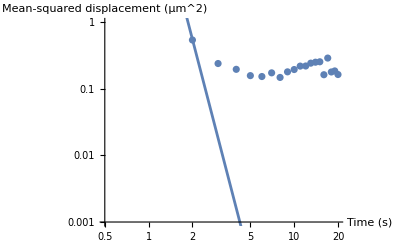

```mathematica
(*  Fast diffusion  *)
DiffS=Table[{FrameTime*n,s3^2*psm^2/.bestfit2xy[[n]]},{n,nmax}];
FitF[a_,b_,t_]:=a*t^b;
BestF=FindFit[DiffS,FitF[a,b,t],{a,b},t];
PlotD=ListLogLogPlot[DiffS,PlotRange->{{FrameTime/2,nmax*FrameTime},{0.001,1}},AxesLabel->{"Time (s)", "Mean-squared displacement (µm^2)"}];
PlotF=LogLogPlot[FitF[a,b,t]/.BestF,{t,0,nmax*FrameTime}];
Print[BestF];
Print[Show[PlotD,PlotF]];
```

```mathematica
(* Apparent diffusion coefficients *)
Line1={{FrameTime/1.5,Mean[Transpose[DiffCoeff][[2]]]},{nmax*FrameTime*1.5,Mean[Transpose[DiffCoeff][[2]]]}};
D1=Mean[Transpose[DiffCoeff][[3]]];Line2={{FrameTime/1.5,D1},{nmax*FrameTime*1.5,D1}};
D2=Mean[Transpose[DiffCoeff][[4]]];Line3={{FrameTime/1.5,D2},{nmax*FrameTime*1.5,D2}};
Lines=ListLogLogPlot[{Line1,Line2,Line3},Joined->True,PlotStyle->Dashed,PlotLabels->{"D = "<>ToString[Mean[Transpose[DiffCoeff][[2]]]]<>" µm^2/s", "D = "<>ToString[Mean[Transpose[DiffCoeff][[3]]]]<>" µm^2/s", "D = "<>ToString[Mean[Transpose[DiffCoeff][[4]]]]<>" µm^2/s"},AxesLabel->{"Time (s)","Apparent diffusion coefficient (μm2/s)"},ImageSize->Large,PlotRange->{{FrameTime/1.5,nmax*FrameTime*1.5},{Mean[Transpose[DiffCoeff][[2]]]/5,Mean[Transpose[DiffCoeff][[4]]]*2}}];
Points=ListLogLogPlot[{Table[{DiffCoeff[[n,1]],DiffCoeff[[n,2]]},{n,1,nmax}],Table[{DiffCoeff[[n,1]],DiffCoeff[[n,3]]},{n,1,nmax}],Table[{DiffCoeff[[n,1]],DiffCoeff[[n,4]]},{n,1,nmax}]}];
Print[Show[Lines,Points]];
```

-Graphics-

Conclusion: It is difficult to assign a clear type of motion to different populations, probably because most of the diffusive motion is caged on the scale of a few seconds, so we have obstructed or caged motion, and also particles might become immobilized or on the contrary start diffusing after an immobilization period (interchange of the different populations).

MEAN-SQUARED DISPLACEMENT CURVES

```mathematica
SegmentedFileCleanZero=SegmentedFileZero[[SantaList]];
```

```mathematica
(*************************** Calculate MSDs *************************************)
(*  Create a file that will hold all the MSD *)
MSDTab=Table[{{0,0}},{i,ntrajClean}];
MSDTabmicron=Table[{{0,0}},{i,ntrajClean}];
(* Create a file that will hold all the result of the fits *)
MSDRes=Table[{},{i,ntrajClean}];
For [i=1, i≤ntrajClean,i++,
n=Length[MegaFileClean[[i]]]; 
MSDLength=MegaFileClean[[i,n,1]]-MegaFileClean[[i,1,1]]; (* Duration of the track (in frames) and length of MSD *)
(* EndToEnd=Sqrt[(MegaFileClean[[i,n,2]]-MegaFileClean[[i,1,2]])^2+(MegaFileClean[[i,n,3]]-MegaFileClean[[i,1,3]])^2]; *)
EndToMax=Max[Table[Sqrt[SegmentedFileCleanZero[[i,k,1]]^2+SegmentedFileCleanZero[[i,k,2]]^2],{k,Length[SegmentedFileCleanZero[[i]]]}]];
(* Make a loop for available time interval *)
For [j = 1, j≤MSDLength, j++,
msdrun=0;counter=0;
For [k=1, k ≤ n-j, k++,  (* Run through all the likely frames and see if the paired one can be found *)
x1=MegaFileClean[[i,k,2]];
y1=MegaFileClean[[i,k,3]];
If[Length[Cases[Transpose[MegaFileClean[[i]]][[1]],MegaFileClean[[i,k,1]]+j]]>0,
x2= MegaFileClean[[i,Flatten[Position[Transpose[MegaFileClean[[i]]][[1]],MegaFileClean[[i,k,1]]+j]],2]][[1]];
y2= MegaFileClean[[i,Flatten[Position[Transpose[MegaFileClean[[i]]][[1]],MegaFileClean[[i,k,1]]+j]],3]][[1]]; 
msdrun=msdrun+(x2-x1)^2+(y2-y1)^2;    (* If so add to the running average  *)
counter++
]
];
If[counter>0,
msdrun=msdrun/counter;
AppendTo[MSDTab[[i]],{j*FrameTime,msdrun*PixelSize^2}];       (* Units are decided here *)
AppendTo[MSDTabmicron[[i]],{j*FrameTime,msdrun*psm^2}]       (* Units are decided here *)
  ];
];
(* Fit the MSD and add the result to TrajInfo *)
DataList=N[Log[10,Drop[MSDTab[[i]],1]]];
DataListShort=Take[DataList,Min[10,Length[DataList]]];   (* Keep only the first 10 points for the fit *)
Fitfunction[betat_,al_,tt_]:=betat+al*tt;
bestfit=FindFit[DataListShort,Fitfunction[betat,al,tt],{{betat,-10},{al,1}},tt];
AppendTo[TrajInfo[[i]],10^(betat/.bestfit)/4]; (* Diffusion coefficient *)
AppendTo[TrajInfo[[i]],al/.bestfit]; (* Anomalous exponent *)
AppendTo[TrajInfo[[i]],EndToMax*psm] (* Maximum total displacement(micron) NOT normalized by track duration (seconds) - just changed *)
];
```

```mathematica
(* All the MSDs on one graph, with limiting behavior *)
t1=FrameTime/1.5;t2=Max[Table[Length[MSDTab[[i]]],{i,Length[MSDTab]}]]*FrameTime*1.5;
t1=1;t2=80;
LineImmobile={{t1,Precisely^2* 10^(-18)},{t2,Precisely^2* 10^(-18)}};
LineBrownian={{t1,4*D1*10^(-12)*t1},{t2,4*D1*10^(-12)*t2}};
Veloce=0.12*10^(-6);
LineDirected={{t1,Veloce^2*t1^2},{t2,Veloce^2*t2^2}};
LinePlot=ListLogLogPlot[{LineImmobile,LineBrownian,LineDirected},Joined->True,PlotStyle->Dashed,PlotRange->{{t1,t2},{10^(-16),10^(-10)}},PlotLabels->{"Immobile particles", "Diffusing particles", "Active particles"},FrameLabel->{"Time (s)","Mean-squared displacement (m^2)"},Frame->True,FrameStyle->{{Directive[20,Black,Thickness[0.003]],Directive[20,White,Thickness[0.003]]},{Directive[20,Black,Thickness[0.003]],Directive[20,White,Thickness[0.003]]}},ImageSize->600];
MSDPlot=ListLogLogPlot[MSDTab,Joined->True,PlotStyle->Thin];
Print[Show[LinePlot,MSDPlot]];
```

-Graphics-

Conclusion: Unsurprisingly, we see a wide range of behavior in individual MSD, from some that reflect immobile behavior, to some that display active directed motion, and every kind diffusive and anomalous diffusive behavior in between.

```mathematica
(* 
(*  Calculation and fit of the average MSD  *)
MSDTabAvTrue=Table[{(n-1)*FrameTime,Mean[Table[Select[MSDTab,Length[#]>=n&][[i,n,2]],{i,Length[Select[MSDTab,Length[#]>=n&]]}]]*10^12},{n,1,nframes-1}];  (* Average of all the curves *)
MSDTabAv=Mean[Select[MSDTabmicron,Length[#]==nframes-1&]];    (* Average of only the long trajectories, used for fitting *)
MSDTabAvShort=Drop[Drop[MSDTabAv,-2],1];
MSDTabAvShortTrue=Drop[Drop[MSDTabAvTrue,-2],1];
MSDPlotAv=ListLogLogPlot[{MSDTabAvShort,MSDTabAvShortTrue},Joined->True,Mesh->All,PlotRange->{{1,60},{2*10^(-3),1.5*10^(0)}},PlotStyle->{Thick && Large},AxesLabel->{"Time (s)","MSD (µm^2/s)"},ImageSize->Large];
LinePlot=ListLogLogPlot[{LineBrownian,LineDirected},Joined->True,PlotStyle->Dashed];
(* Model including a fraction p of particles undergoing directed motion *)
Fitfunction[Diff_,p_,Vel_,Err_,t_]:=4*Diff*t+p*Vel^2*t^2+Err^2;
(* Model including anomalous/caged diffusion *)
Fitfunction2All[Diff_,al_,Err_,t_]:=4*Diff*t^al+Err^2;
bestfit=FindFit[MSDTabAvShort,Fitfunction[Diff,0,0,Err,tt],{{Diff,D1},{Err,(Precisely*10^(-3))}},tt,WorkingPrecision->5,MaxIterations->1000];
FitPlot=LogLogPlot[Fitfunction[Diff,0,0,Err,tt]/.bestfit,{tt,0.1,60},PlotStyle->Green];
bestfit2=FindFit[MSDTabAvShort,Fitfunction2All[Diff,al,Precisely*10^(-3),tt],{{Diff,D1},{al,0.6}},tt,WorkingPrecision->5,MaxIterations->1000];
FitPlot2=LogLogPlot[Fitfunction2All[Diff,al,Precisely*10^(-3),tt]/.bestfit2,{tt,0.1,60},PlotStyle->Red];
Print["Result of the normal diffusion fit (green) - variable error:", bestfit];
Print["Result of the anomalous diffusion fit (red) - fixed error:", bestfit2];
(* Orange: All the curves, Blue: Only the long curves *)
Show[MSDPlotAv,FitPlot,FitPlot2]
*)
```

Conclusion: It is not clear that averaging all the curves is meaningful, since different averaging leads very different results. Which is why below we sort the curves first, then average different categories.

VELOCITIES AUTOCORRELATION FUNCTIONS

```mathematica
(*************************** Calculate VAFs *************************************)
VAFTab=Table[{},{i,ntrajClean}];    (* Table that will hold the VAF for each trajectory *)
VAFTab1=Table[{},{i,ntrajClean}];      (* Table that will hold the values of all the first VAF coefficients for each trajectory *)
MaxVAF=0;                                                             (* Maximum value of the VAF *)
For [i=1, i≤ntrajClean,i++,
(* decide on the length of the VAF (largest possible lag time *)
n=Length[PlotVelocities[[i]]];
VAFLength=PlotVelocities[[i,n,1]]-PlotVelocities[[i,1,1]];
(* Make a loop for available time interval *)
For [j = 0, j≤VAFLength, j++,
(* Run through all the likely frames and see if the paired one can be found *)
vafrun=0;counter=0;
For [k=1, k ≤ n-j, k++,
vx1=PlotVelocities[[i,k,2]];
vy1=PlotVelocities[[i,k,3]];
If[Length[Cases[Transpose[PlotVelocities[[i]]][[1]],PlotVelocities[[i,k,1]]+j]]>0,
vx2= PlotVelocities[[i,Flatten[Position[Transpose[PlotVelocities[[i]]][[1]],PlotVelocities[[i,k,1]]+j]],2]][[1]];
vy2= PlotVelocities[[i,Flatten[Position[Transpose[PlotVelocities[[i]]][[1]],PlotVelocities[[i,k,1]]+j]],3]][[1]]; 
(* If so add to the running average  *)
VAF=vx1*vx2+vy1*vy2; If[VAF>MaxVAF,MaxVAF=VAF]; If[j==1,VAFTab1[[i]]=AppendTo[VAFTab1[[i]],VAF]];
vafrun=vafrun+VAF;
counter++
]
(* Close the loop *)
];
If[counter>0,
vafrun=vafrun/counter;
AppendTo[VAFTab[[i]],{j*FrameTime,vafrun}]       (* time is in seconds now *)
  ];
];
TrajInfo[[i]]=AppendTo[TrajInfo[[i]],VAFTab[[i,2,2]]];    (* Record the value of the VAF at t=FrameTime *)
TrajInfo[[i]]=AppendTo[TrajInfo[[i]],Max[VAFTab1[[i]]]]    (* Record the value of the VAF at t=FrameTime *)
];
```

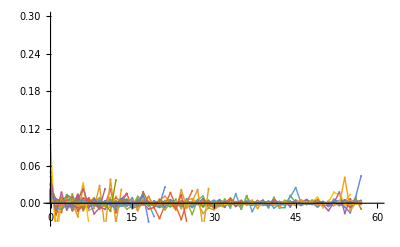

```mathematica
(****************** Plot all the VAFs on one graph ***************************)
Print[ListPlot[VAFTab,Joined->True,Mesh->All,PlotRange->{{0,60},{-0.03,0.3}},PlotStyle->Thin]];
```

Mean value of the VAF -0.00408614

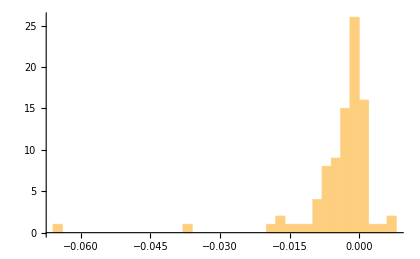

```mathematica
(******* Distribution of VAF values at a certain time point *)
n=2;
VAFTabsh=Select[VAFTab,Length[#]>=n&];
TestTable=Table[VAFTabsh[[i,n,2]],{i,Length[VAFTabsh]}];
Print["Mean value of the VAF ",Mean[TestTable]];
Print[Histogram[TestTable,PlotRange->Full]];
```

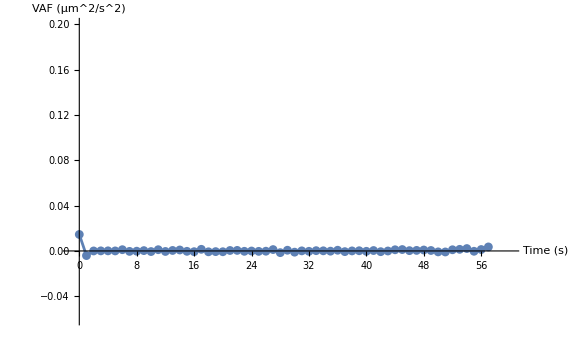

```mathematica
(****** Plot the average VAF *******)
VAFTabTrueAv=Table[{(n-1)*FrameTime,Mean[Table[Select[VAFTab,Length[#]>=n&][[i,n,2]],{i,Length[Select[VAFTab,Length[#]>=n&]]}]]},{n,1,nframes-1}];
VAFPlotAv=ListPlot[VAFTabTrueAv,Joined->True,Mesh->All,PlotRange->{{-1,60},{-0.06,0.2}},PlotStyle->{Thick && Large},AxesLabel->{"Time (s)","VAF (µm^2/s^2)"},ImageSize->Large];
Print[VAFPlotAv];
```

Conclusion: The average VAF is slightly negative close to the origin, maybe a trace of confined trajectories. As for the MSDs, it will be a better exercise once the curves have been sorted.

TRAJECTORY CLASSIFICATION

```mathematica
(* Trajectory classification *)
Crazy=MaxDisplacement;     (* Limit for the maximum allowed displacement in pixel *)
DirectedLimit=bound2*0.5; 
(* DirectedLimitStep=bound2/psm*4; *)
AlphaLimit=1.1;
ImmobileLimit=bound1*4;
ImmobileLimitStep=bound1/psm*4;
FactiveLimit=0.5;   (* Limit fraction of active moves to be considered directed *)
(* Create tables that will hold trajectories for different categories of motion *)
TrajInfoDirected={}; (* For directed trajectories *)
TrajInfoBrownian={};(* For Brownian trajectories *)
TrajInfoImmobile={}; (* For immobile trajectories *)
TrajInfoCrazy={};  (* For crazy trajectories *)
(* Look at each different trajectory and classify it *)
For [i=1, i≤ntrajClean,i++,
If[TrajInfo[[i]][[5]]>Crazy,
AppendTo[TrajInfoCrazy,TrajInfo[[i]]],    (* Crazy trajectories are those with displacements that are too large (note: at the moment this is taken care of before so there are no crazy trajectories) *)
If[((* (TrajInfo[[i,15]]/(TrajInfo[[i,2]]*FrameTime)>DirectedLimit *) TrajInfo[[i,15]]>(DirectedLimit*Sqrt[TrajInfo[[i,2]]])  ||TrajInfo[[i,14]]>AlphaLimit(*TrajInfo[[i]][[5]]>DirectedLimitStep*) 
      (*||TrajInfo[[i]][[12]]>FactiveLimit *)   (* && TrajInfo[[i]][[16]]>0 *)    ) ,
AppendTo[TrajInfoDirected,TrajInfo[[i]]],  (* Directed trajectories are those with a certain average displacement, or with a non-zero number of active moves (AND with a positive VAF) *)
If[TrajInfo[[i,15]]<ImmobileLimit && TrajInfo[[i]][[5]]<ImmobileLimitStep  (*TrajInfo[[i]][[4]]<ImmobileLimitStep*)(* TrajInfo[[i]][[10]]>0.5 *),
AppendTo[TrajInfoImmobile,TrajInfo[[i]]],   (* Immobile trajectories are those who remain within a certain region and never have any long step *)
AppendTo[TrajInfoBrownian,TrajInfo[[i]]]]   (* Brownian trajectories are all the others *)
]
]
]

(* Make lists containing the trajectory id numbers of different types of trajectories *)
If[Length[TrajInfoBrownian]>0,SantaListBrownian=Transpose[TrajInfoBrownian][[1]],SantaListBrownian={}]; 
If[Length[TrajInfoImmobile]>0,SantaListImmobile=Transpose[TrajInfoImmobile][[1]],SantaListImmobile={}]; 
If[Length[TrajInfoDirected]>0,SantaListDirected=Transpose[TrajInfoDirected][[1]],SantaListDirected={}]; 

(* Make lists containing the trajectory id numbers of different types of trajectories in SantaList *)
BrownianList={}; For[i=1,i≤Length[TrajInfoBrownian],i++,
BrownianList=AppendTo[BrownianList,Flatten[Position[SantaList,TrajInfoBrownian[[i,1]]]][[1]]]];   
ImmobileList={}; For[i=1,i≤Length[TrajInfoImmobile],i++,
ImmobileList=AppendTo[ImmobileList,Flatten[Position[SantaList,TrajInfoImmobile[[i,1]]]][[1]]]];
DirectedList={}; For[i=1,i≤Length[TrajInfoDirected],i++,
DirectedList=AppendTo[DirectedList,Flatten[Position[SantaList,TrajInfoDirected[[i,1]]]][[1]]]];
```

```mathematica
(* DataP=ListPlot[binneddistriberr1,PlotRange->{{0,0.5},{0,20.5}},PlotStyle->Black,Frame->True,FrameStyle->{{Directive[20,Black,Thickness[0.003]],Directive[20,White,Thickness[0.003]]},{Directive[20,Black,Thickness[0.003]],Directive[20,White,Thickness[0.003]]}},FrameLabel->{"Step size, δr (μm)","Probability density, p(δr)"},ImageSize->600]; *)
```

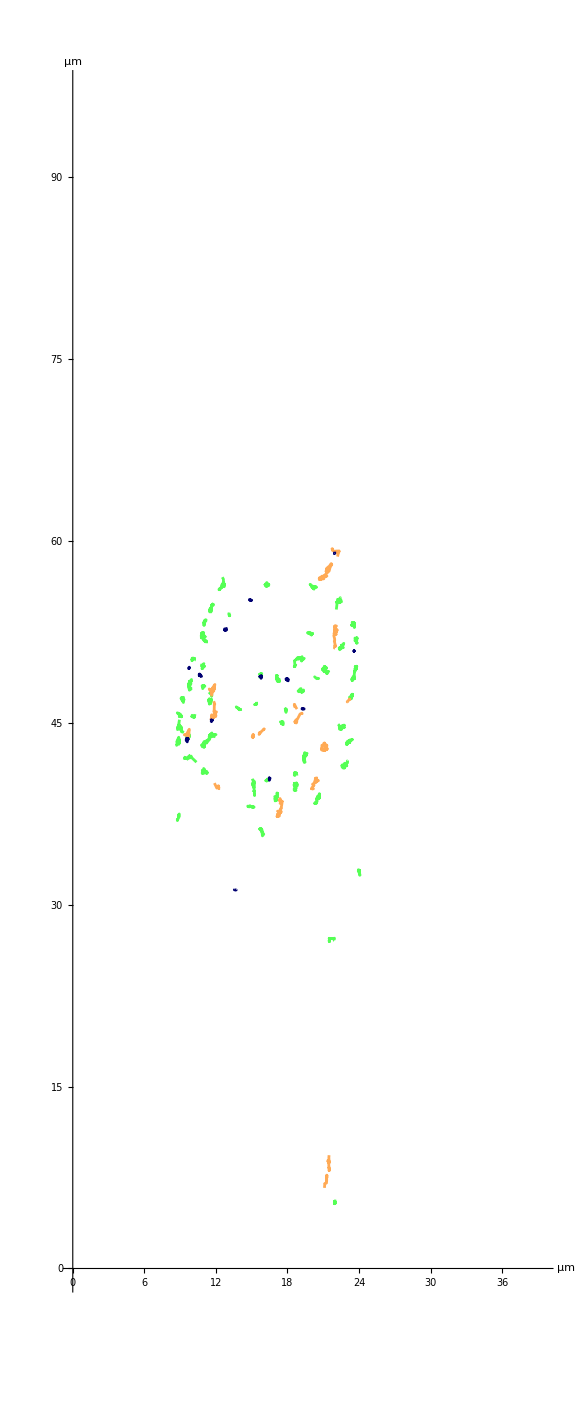

Total number of trajectories: 90

Number of crazy trajectories: 0

Number of immobile trajectories: 13

Number of Brownian trajectories: 60

Number of directed trajectories: 17

```mathematica
(* Visualisation of the classified trajectories *)
SegmentedFileCleanB=SegmentedFile[[SantaListBrownian]];
SegmentedFileCleanI=SegmentedFile[[SantaListImmobile]];
SegmentedFileCleanD=SegmentedFile[[SantaListDirected]];
xpos=0; ypos= 0; xpos0=0; ypos0=0; size=nymax;
nymax=ny*psm;  nxmax=nx*psm;   (* Maximum possible x and y valuex in microns *)
Tra=ListPlot[SegmentedFileCleanB*psm,PlotRange->{{0,nxmax},{0,nymax}},AspectRatio->ny/nx,Joined->True,ImageSize->Large,AxesLabel->{"μm","μm"}(* ,Epilog->Inset[SetAlphaChannel[Frame1,0.3],{xpos,ypos},{xpos0,ypos0},size]*),PlotStyle->{color2}];
If[Length[TrajInfoDirected]>0,
TraD=ListPlot[SegmentedFileCleanD*psm,PlotRange->{{0,nxmax},{0,nymax}},AspectRatio->ny/nx,Joined->True,ImageSize->Large,AxesLabel->{"μm","μm"},PlotStyle->{color3}],TraD={}];
If[Length[TrajInfoImmobile]>0,TraI=ListPlot[SegmentedFileCleanI*psm,PlotRange->{{0,nxmax},{0,nymax}},AspectRatio->ny/nx,Joined->True,ImageSize->Large,AxesLabel->{"μm","μm"},PlotStyle->{color1}],TraI={}];
Print[Show[Tra,TraD,TraI]];
(* Print a summary of the results of the classification *)
Print["Total number of trajectories: ",Length[TrajInfo]];
Print["Number of crazy trajectories: ",Length[TrajInfoCrazy]]
Print["Number of immobile trajectories: ",Length[TrajInfoImmobile]];
Print["Number of Brownian trajectories: ",Length[TrajInfoBrownian]];
Print["Number of directed trajectories: ",Length[TrajInfoDirected]];
(* Brownian trajectories are blue, immobile trajectories are dark blue and directed trajectories are orange *)
```

```mathematica
(* TrajInfo: (1) Trajectory #, (2) Trajectory length (frame), (3) Average, (4) min, and (5) max 1-step displacement (pixel), (6) number of 1-frame intervals, (7) number of immobile moves, (8) diffusing moves and (9) active moves, (10) fraction of immobile moves, (11) diffusing moves and (12) active moves, (13) diffusion coefficient, (14) anomalous exponent, (15)total displacement (micron), (16) Value of the average VAF at t = FrameTime (17) Max individual value of the VAF at t = FrameTime   *)
```

```mathematica
(******* Construction of Output File *******)

If[DetailedOutput,
OutputFile3={{{"Immobile Trajectories"},{"Trajectory #", "Trajectory Length (number of frames)", "Diffusion coefficient D (10^{-3} μm^2/s)", "Anomalous exponent α","VAF (1) μm^2/s^2"}},{{"Brownian Trajectories"},{"Trajectory # - Brownian", "Trajectory Length (number of frames)", "Diffusion coefficient, D (10^{-3} μm^2/s)", "Anomalous exponent, α","VAF (1) μm^2/s^2"}},{{"Directed Trajectories"},{"Trajectory # - Directed", "Trajectory Length (number of frames)", "Maximum velocity v (μm/s)", "Anomalous exponent α","VAF (1) μm^2/s^2"}}};
For[i=1,i<=Length[TrajInfo[[ImmobileList]]],i++,AppendTo[OutputFile3[[1]],{i,TrajInfo[[ImmobileList]][[i,2]],TrajInfo[[ImmobileList]][[i,13]]*10^15,TrajInfo[[ImmobileList]][[i,14]],TrajInfo[[ImmobileList]][[i,16]]}]];
For[i=1,i<=Length[TrajInfo[[BrownianList]]],i++,AppendTo[OutputFile3[[2]],{i,TrajInfo[[BrownianList]][[i,2]],TrajInfo[[BrownianList]][[i,13]]*10^15,TrajInfo[[BrownianList]][[i,14]],TrajInfo[[BrownianList]][[i,16]]}]];
For[i=1,i<=Length[TrajInfo[[DirectedList]]],i++,AppendTo[OutputFile3[[3]],{i,TrajInfo[[DirectedList]][[i,2]],Sqrt[TrajInfo[[DirectedList]][[i,17]]],TrajInfo[[DirectedList]][[i,14]],TrajInfo[[DirectedList]][[i,16]]}]];
Export[NotebookDirectory[]<>DirName<>"/Output_"<>FileName<>"_"<>"TrajectoryAnalysis.xlsx",OutputFile3]
]
```

/Users/cecile/Dropbox/1-NEW/RESEARCH/PROJECTS/MTB/Donna/5b-MTB_VesicleTrajectories/Code//Output_Traj_mamLnew10_TrajectoryAnalysis.xlsx

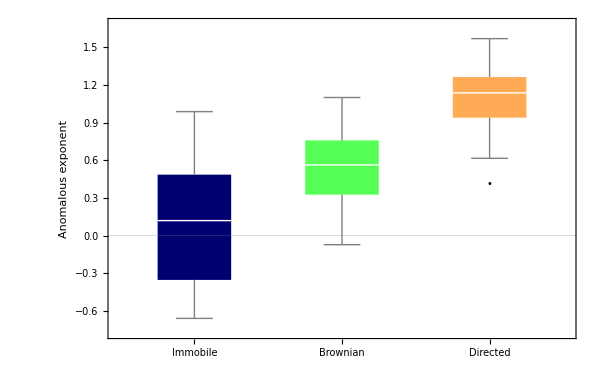

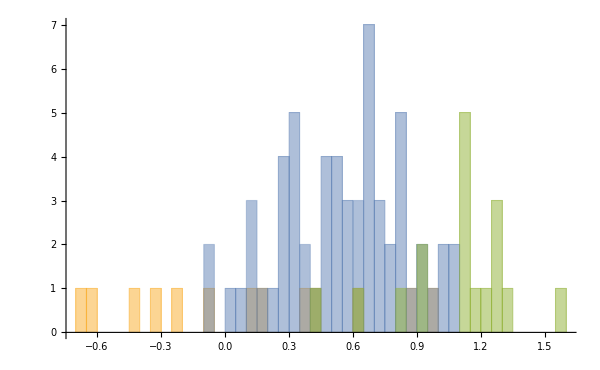

```mathematica
(******* Histogram of alpha values *********)
Data1alpha=Transpose[TrajInfo[[ImmobileList]]][[14]];Data2alpha=Transpose[TrajInfo[[BrownianList]]][[14]];Data3alpha=Transpose[TrajInfo[[DirectedList]]][[14]];
BoxWhiskerChart[{Data1alpha,Data2alpha,Data3alpha},"Outliers",ChartLabels->{"Immobile","Brownian","Directed"},FrameLabel->{"","Anomalous exponent"},ChartStyle->{color1,color2,color3},PlotTheme->"Scientific",ImageSize->600,FrameStyle->Directive[Black, 24,Thickness[0.002]]]
Histogram[{Transpose[TrajInfo[[ImmobileList]]][[14]],Transpose[TrajInfo[[BrownianList]]][[14]],Transpose[TrajInfo[[DirectedList]]][[14]]},{0.05}]
```

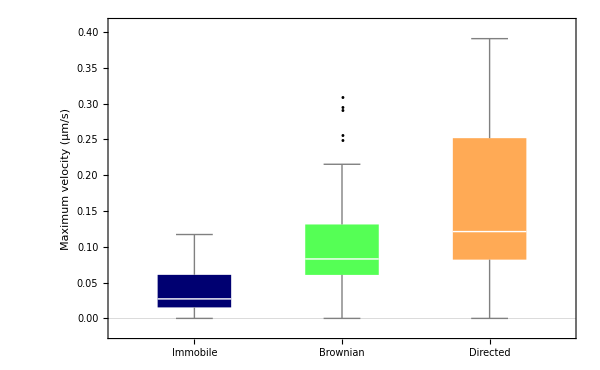

```mathematica
(* Distributions of the square root of the maximum values for the VAF at t = FrameTime for each trajectory (gives a proxy for the max velocity for directed trajectories *)
Data1Vel=Re[Sort[Sqrt[Transpose[TrajInfoImmobile][[17]]]]];Data2Vel=Re[Sort[Sqrt[Transpose[TrajInfoBrownian][[17]]]]];Data3Vel=Re[Sort[Sqrt[Transpose[TrajInfoDirected][[17]]]]];BoxWhiskerChart[{Data1Vel,Data2Vel,Data3Vel},"Outliers",ChartLabels->{"Immobile","Brownian","Directed"},FrameLabel->{"","Maximum velocity (µm/s)"},ChartStyle->{color1,color2,color3},PlotTheme->"Scientific",ImageSize->600,FrameStyle->Directive[Black, 24,Thickness[0.002]]]
```

```mathematica
(**** Average values of fit parameters for  different types of trajectory ******)
Print["Immobile particles:"];
Print[" Average/Median D: ",Mean[Transpose[TrajInfo[[ImmobileList]]][[13]]*10^(15)],"/",Median[Transpose[TrajInfo[[ImmobileList]]][[13]]*10^(15)]," x 10^-3 µm^2/s,    Average/Median α: ",Mean[Transpose[TrajInfo[[ImmobileList]]][[14]]],"/", Median[Transpose[TrajInfo[[ImmobileList]]][[14]]] ];
Print["Brownian particles:"];
Print[" Average/Median D: ",Mean[Transpose[TrajInfo[[BrownianList]]][[13]]*10^(15)],"/",Median[Transpose[TrajInfo[[BrownianList]]][[13]]*10^(15)]," x 10^-3 µm^2/s,    Average/Median α: ",Mean[Transpose[TrajInfo[[BrownianList]]][[14]]],"/", Median[Transpose[TrajInfo[[BrownianList]]][[14]]] ];
Print["Directed particles:"];
Print["Average/Median α: ",Mean[Transpose[TrajInfo[[DirectedList]]][[14]]],"/", Median[Transpose[TrajInfo[[DirectedList]]][[14]]] ];
Print["Average/Median maximum velocity (srqt[max[VAF[1]]) (µm/s): ",Mean[Data3Vel],"/", Median[Data3Vel] ];
Print["All particles"]; 
Print[" Average/Median D: ",Mean[Transpose[TrajInfo][[13]]*10^(15)],"/",Median[Transpose[TrajInfo][[13]]*10^(15)]," x 10^-3 µm^2/s,    Average/Median α: ",Mean[Transpose[TrajInfo][[14]]],"/", Median[Transpose[TrajInfo][[14]]] ];
```

Immobile particles:

Average/Median D: 2.51567/2.1756 x 10^-3 µm^2/s,    Average/Median α: 0.0918364/0.119134

Brownian particles:

Average/Median D: 3.34727/2.87853 x 10^-3 µm^2/s,    Average/Median α: 0.54643/0.562453

Directed particles:

Average/Median α: 1.08652/1.13618

Average/Median maximum velocity (srqt[max[VAF[1]]) (µm/s): 0.163878/0.121255

All particles

Average/Median D: 3.40722/2.81419 x 10^-3 µm^2/s,    Average/Median α: 0.582784/0.625962

```mathematica
If[Output,OutputFile4={{"DirectedLimit (µm)",DirectedLimit},{"AlphaLimit",AlphaLimit},{"ImmobileLimit (µm)",ImmobileLimit},{"ImmobileLimitStep (pixel)",ImmobileLimitStep},{"FactiveLimit",FactiveLimit},
{"Median diffusion coefficient - all particles (um^2/s)",Median[Transpose[TrajInfo][[13]]*10^(12)]},{"Median anomalous exponent - all particles",Median[Transpose[TrajInfo][[14]]] },{"Median diffusion coefficient - immobile particles (um^2/s)",Median[Transpose[TrajInfo[[ImmobileList]]][[13]]*10^(12)]},{"Median anomalous exponent - immobile particles",Median[Transpose[TrajInfo[[ImmobileList]]][[14]]]},{"Median diffusion coefficient - Brownian particles (um^2/s)",Median[Transpose[TrajInfo[[BrownianList]]][[13]]*10^(12)]},{"Median anomalous exponent - Brownian particles",Median[Transpose[TrajInfo[[BrownianList]]][[14]]]},
{"Median anomalous exponent - Directed particles",Median[Transpose[TrajInfo[[DirectedList]]][[14]]]},{"Median velocity - Directed particles (µm/s)",Median[Data3Vel]}}];
```

```mathematica
(******* Calculate a version of all the trajectories with the same start point ***********)
SegmentedFileCleanZero=SegmentedFileZero[[SantaList]];
LL=Length[SegmentedFileCleanZero];
xmaxclean=Max[Table[Max[Transpose[SegmentedFileCleanZero[[i]]][[1]]],{i,LL}]]*psm;
xminclean=Min[Table[Min[Transpose[SegmentedFileCleanZero[[i]]][[1]]],{i,LL}]]*psm;
ymaxclean=Max[Table[Max[Transpose[SegmentedFileCleanZero[[i]]][[2]]],{i,LL}]]*psm;
yminclean=Min[Table[Min[Transpose[SegmentedFileCleanZero[[i]]][[2]]],{i,LL}]]*psm;
xymax=Max[xmaxclean,-xminclean,ymaxclean,-yminclean];
AllTraj=ListPlot[SegmentedFileCleanZero*psm,PlotRange->{{-xymax,xymax},{-xymax,xymax}},AspectRatio->1,Joined->True,Mesh->All,ImageSize->Large,AxesLabel->{"μm","μm"}];
```

```mathematica
Print[OutputFile4];
```

OutputFile4

```mathematica
(****** Chose how many points will be fit for the MSD and plot parameters **********)
nPMSD=12;
xyM=3.9;
VAFm=-0.02;VAFM=0.05;
```

~~~Immobile Trajectories

```mathematica
DataP=ListPlot[binneddistriberr1,PlotRange->{{0,0.5},{0,20.5}},PlotStyle->Black,Frame->True,FrameStyle->{{Directive[20,Black,Thickness[0.003]],Directive[20,White,Thickness[0.003]]},{Directive[20,Black,Thickness[0.003]],Directive[20,White,Thickness[0.003]]}},FrameLabel->{"Step size, δr (μm)","Probability density, p(δr)"},ImageSize->600];
```

Number of trajectories showing immobile or constrained motion: 13

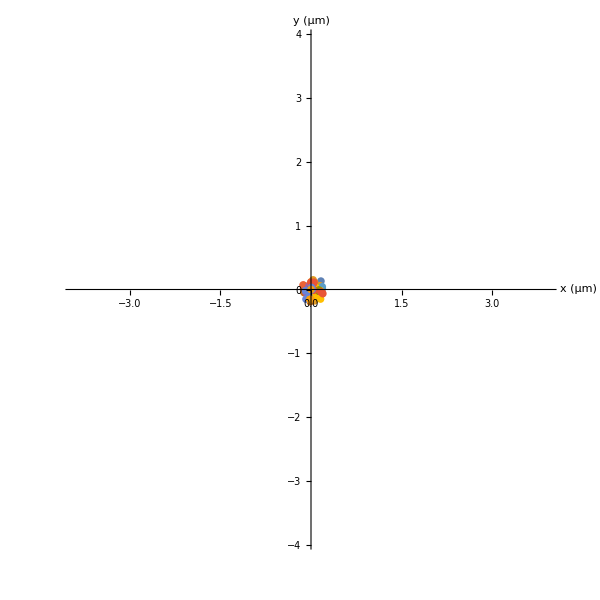

```mathematica
(*  Immobile trajectories  *)
If[Length[TrajInfoImmobile]>0,
SegmentedFileCleanImmobileZero=SegmentedFileZero[[Transpose[TrajInfoImmobile][[1]]]];
Print["Number of trajectories showing immobile or constrained motion: ",Length[TrajInfoImmobile]];
plim=ImmobileLimit/psm*FrameTime*50; plim=xymax; plim=xyM;
PlotTrajIm=ListPlot[SegmentedFileCleanImmobileZero*psm,PlotRange->{{-plim,plim},{-plim,plim}},AspectRatio->1,Joined->True,Mesh->All,ImageSize->600,AxesLabel->{"x (μm)","y (μm)"},AxesStyle->Directive[Black, 20,Thickness[0.002]]];
Print[PlotTrajIm]
];
```

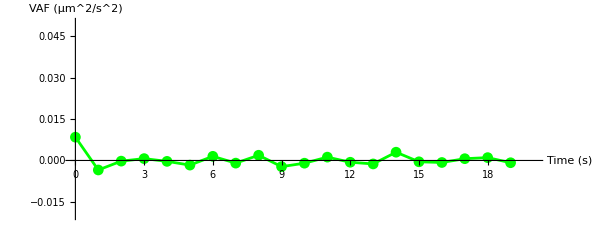

```mathematica
(****** Plot the average VAF *******)
If[Length[TrajInfoImmobile]>0,
VAFTabI=VAFTab[[ImmobileList]];        (* MSD corresponding to immobile trajectories *)
VAFTabTrueAvI=Table[{(n-1)*FrameTime,Mean[Table[Select[VAFTabI,Length[#]>=n&][[i,n,2]],{i,Length[Select[VAFTabI,Length[#]>=n&]]}]]},{n,1,nframes-3}];
Vm=Min[Transpose[VAFTabTrueAvI][[2]]]*1.2;VM=Max[Transpose[VAFTabTrueAvI][[2]]]*1.2;
Vm=VAFm;VM=VAFM;
VAFPlotAvI=ListPlot[VAFTabTrueAvI,PlotRange->{{-0.01,20},{Vm,VM}},AspectRatio->0.4,Joined->True,Mesh->All,ImageSize->600,PlotStyle->{Green},AxesLabel->{"Time (s)","VAF (µm^2/s^2)"},AxesStyle->Directive[Black, 18,Thickness[0.002]]];
Print[VAFPlotAvI];
FirstPointI=VAFTabTrueAvI[[1,2]];SecondPointI=VAFTabTrueAvI[[2,2]];
]
```

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (5).

Result of the normal diffusion fit (black) - variable error:{Diff→0.00012411,Err→0.095895}

Result of the anomalous diffusion fit (red) - fixed error:{Diff→0.001211,al→0.32,Err→0.062132}

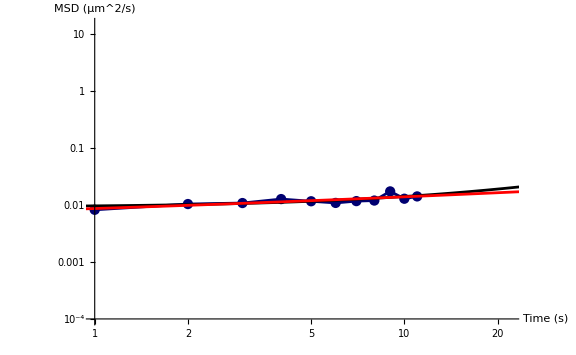

```mathematica
(*  Calculation and fit of the average MSD  *)
If[Length[TrajInfoImmobile]>0,
MSDTabI=MSDTab[[ImmobileList]];        (* MSD corresponding to immobile trajectories *)
MM=Max[Table[Length[MSDTabI[[i]]],{i,Length[MSDTabI]}]];      (* Length of the longer immobile trajectories *)
MSDTabAvTrue=Table[{(n-1)*FrameTime,Mean[Table[Select[MSDTabI,Length[#]>=n&][[i,n,2]],{i,Length[Select[MSDTabI,Length[#]>=n&]]}]]*10^12},{n,MM}];  (* Average of all the curves *)
MSDTabAvShortTrueI=Drop[Take[MSDTabAvTrue,nPMSD],1];
MSDPlotAvI=ListLogLogPlot[MSDTabAvShortTrueI,Joined->True,Mesh->All,PlotRange->{{1,(nPMSD+10)*FrameTime},{1*10^(-4),1.5*10^(1)}},PlotStyle->{Thick && Large,color1},AxesLabel->{"Time (s)","MSD (µm^2/s)"},ImageSize->Large];
LinePlot=ListLogLogPlot[{LineBrownian,LineDirected},Joined->True,PlotStyle->Dashed];
(* Model including a fraction p of particles undergoing directed motion *)
FitfunctionI[Diff_,p_,Vel_,Err_,t_]:=4*Diff*t+p*Vel^2*t^2+Err^2;
(* Model including anomalous/caged diffusion *)
Fitfunction2I[Diff_,al_,Err_,t_]:=4*Diff*t^al+Err^2;
bestfit=FindFit[MSDTabAvShortTrueI,{FitfunctionI[Diff,0,0,Err,tt],Err>0},{{Diff,D1},{Err,(Precisely*10^(-3))}},tt,WorkingPrecision->5,MaxIterations->1000];
FitPlotI=LogLogPlot[FitfunctionI[Diff,0,0,Err,tt]/.bestfit,{tt,0.1,60},PlotStyle->Black];   (* Fit diffusive particles with localization error *)
bestfit2=FindFit[MSDTabAvShortTrueI,Fitfunction2I[Diff,al,Err,tt],{{Diff,D1},{al,0.6},{Err,(Precisely*10^(-3))}},tt,WorkingPrecision->5,MaxIterations->1000];
FitPlot2I=LogLogPlot[Fitfunction2I[Diff,al,Err,tt]/.bestfit2,{tt,0.1,60},PlotStyle->Red];
Print["Result of the normal diffusion fit (black) - variable error:", bestfit];
Print["Result of the anomalous diffusion fit (red) - fixed error:", bestfit2];
Print[Show[MSDPlotAvI,FitPlotI,FitPlot2I]];
]
If[Output,OutputFile5={{"Immobile trajectories",Length[TrajInfoImmobile]},{"Cage size/localization precision (µm)",Err/.bestfit},{"Diffusion coefficient of immobile particles (µm^2/s)",Diff/.bestfit},{"VAF Immobile (t=0)",FirstPointI},{"VAF Immobile (t=1 frame)",SecondPointI}}];
```

```mathematica
Print[OutputFile5];
```

OutputFile5

~~~Brownian trajectories

Number of trajectories showing pure Brownian motion: 60

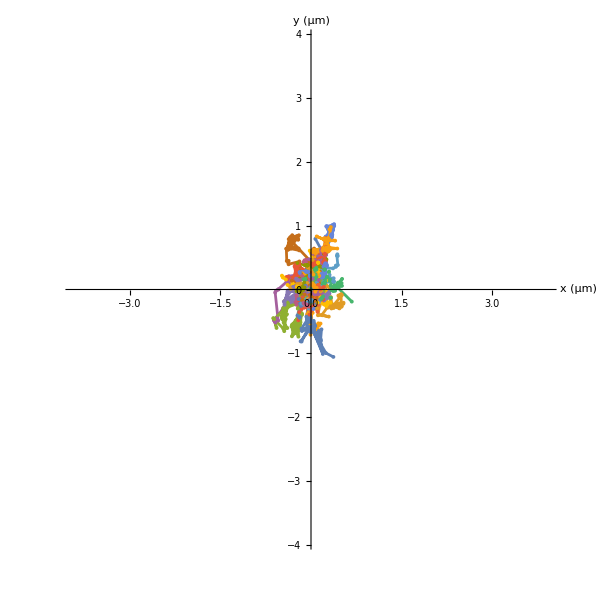

```mathematica
(*  Brownian trajectories  *)
SegmentedFileCleanBrownianZero=SegmentedFileZero[[Transpose[TrajInfoBrownian][[1]]]];
Print["Number of trajectories showing pure Brownian motion: ",Length[TrajInfoBrownian]];
plim=xymax;plim=xyM;
ListPlot[SegmentedFileCleanBrownianZero*psm,PlotRange->{{-plim,plim},{-plim,plim}},AspectRatio->1,Joined->True,Mesh->All,ImageSize->600,AxesLabel->{"x (μm)","y (μm)"},AxesStyle->Directive[Black, 20,Thickness[0.002]]]
```

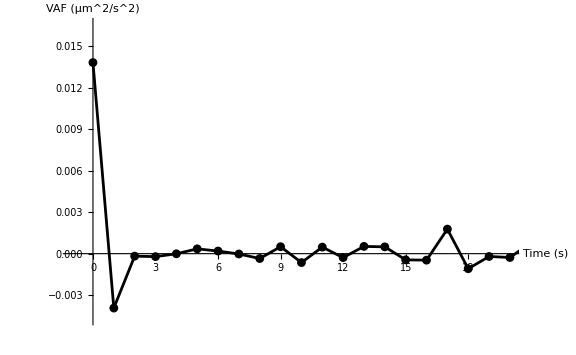

```mathematica
(****** Plot the average VAF *******)
VAFTabB=VAFTab[[BrownianList]];        (* VAF corresponding to Brownian trajectories *)
VAFTabTrueAvB=Table[{(n-1)*FrameTime,Mean[Table[Select[VAFTabB,Length[#]>=n&][[i,n,2]],{i,Length[Select[VAFTabB,Length[#]>=n&]]}]]},{n,1,nframes-3}];
VAFPlotAvB=ListPlot[VAFTabTrueAvB,Joined->True,Mesh->All,PlotRange->{{-1,20},{Min[Transpose[VAFTabTrueAvB][[2]]]*1.2,Max[Transpose[VAFTabTrueAvB][[2]]]*1.2}},PlotStyle->{Black},AxesLabel->{"Time (s)","VAF (µm^2/s^2)"},ImageSize->Large];
Print[VAFPlotAvB];
FirstPointB=VAFTabTrueAvB[[1,2]];SecondPointB=VAFTabTrueAvB[[2,2]];
```

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (5).

Result of the normal diffusion fit (green):{Diff→0.00092337,Err→0.1092}

Result of the anomalous diffusion fit (black):{Diff→0.0016662,al→0.782,Err→0.088375}

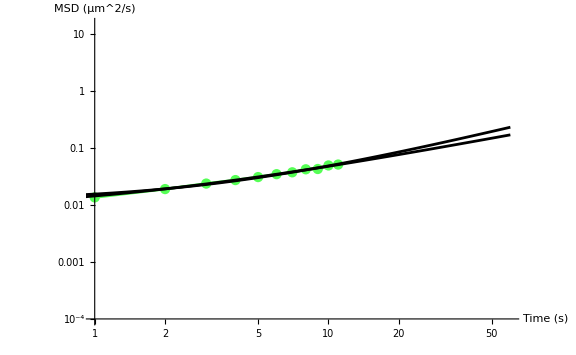

```mathematica
(*  Calculation and fit of the average MSD  *)
MSDTabB=MSDTab[[BrownianList]];        (* MSD corresponding to Brownian trajectories *)
MM=Max[Table[Length[MSDTabB[[i]]],{i,Length[MSDTabB]}]];      (* Length of the longer immobile trajectories *)
MSDTabAvTrue=Table[{(n-1)*FrameTime,Mean[Table[Select[MSDTabB,Length[#]>=n&][[i,n,2]],{i,Length[Select[MSDTabB,Length[#]>=n&]]}]]*10^12},{n,MM}];  (* Average of all the curves *)
MSDTabAvShortTrueB=Drop[Take[MSDTabAvTrue,nPMSD],1];
MSDPlotAvB=ListLogLogPlot[MSDTabAvShortTrueB,Joined->True,Mesh->All,PlotRange->{{1,60},{1*10^(-4),1.5*10^(1)}},PlotStyle->{Thick && Large,color2},AxesLabel->{"Time (s)","MSD (µm^2/s)"},ImageSize->Large];
LinePlot=ListLogLogPlot[{LineBrownian,LineDirected},Joined->True,PlotStyle->Dashed];
(* Model including a fraction p of particles undergoing directed motion *)
FitfunctionB[Diff_,p_,Vel_,Err_,t_]:=4*Diff*t+p*Vel^2*t^2+Err^2;
(* Model including anomalous/caged diffusion *)
Fitfunction2B[Diff_,al_,Err_,t_]:=4*Diff*t^al+Err^2;
bestfit=FindFit[MSDTabAvShortTrueB,FitfunctionB[Diff,0,0,Err,tt],{{Diff,D1},{Err,(Precisely*10^(-3))}},tt,WorkingPrecision->5,MaxIterations->1000];
FitPlotB=LogLogPlot[FitfunctionB[Diff,0,0,Err,tt]/.bestfit,{tt,0.1,60},PlotStyle->Black];
bestfit2=FindFit[MSDTabAvShortTrueB,{Fitfunction2B[Diff,al,Err,tt],Err>0&&Diff>0&&al>0},{{Diff,D1},{al,0.6},{Err,(Precisely*10^(-3))}},tt,WorkingPrecision->5,MaxIterations->1000];
FitPlot2B=LogLogPlot[Fitfunction2B[Diff,al,Err,tt]/.bestfit2,{tt,0.1,60},PlotStyle->Black];
Print["Result of the normal diffusion fit (green):", bestfit];
Print["Result of the anomalous diffusion fit (black):", bestfit2];
Show[MSDPlotAvB,FitPlotB,FitPlot2B]
If[Output,OutputFile6={{"Brownian trajectories",Length[TrajInfoBrownian]},{"Cage size/localization precision (µm)",Err/.bestfit2},{"Apparent diffusion coefficient of Brownian particles for t=1s (µm^2/s)",Diff/.bestfit2},{"Anomalous exponent",al/.bestfit2},{"VAF Brownian (t=0)",FirstPointB},{"VAF Brownian (t=1 frame)",SecondPointB}}];
```

```mathematica
Print["For individual trajectories, the median diffusion coefficient is: ", Median[Transpose[TrajInfoBrownian][[13]]]*10^12," µm^2/s"];
Print["And the median anomalous exponent is: ", Median[Transpose[TrajInfoBrownian][[14]]],"."];
```

For individual trajectories, the median diffusion coefficient is: 0.00287853 µm^2/s

And the median anomalous exponent is: 0.562453.

```mathematica
If[Output,Print[OutputFile6]];
```

~~~Directed trajectories

Number of trajectories showing active motion: 17

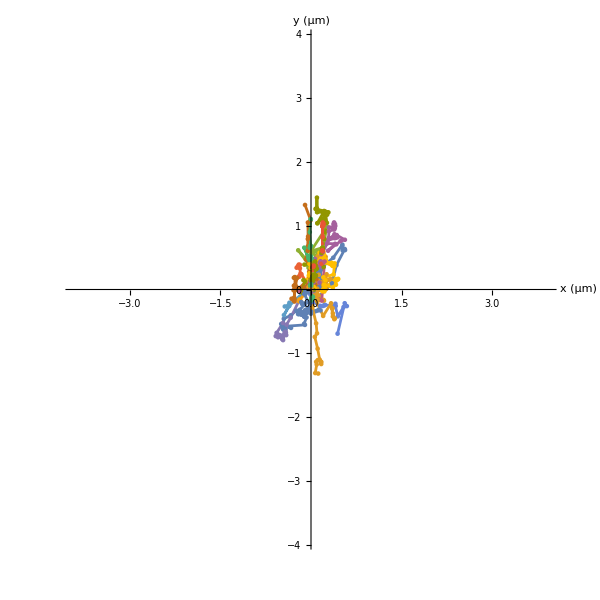

```mathematica
(*   Directed trajectories   *)
If[Length[TrajInfoDirected]>0,
SegmentedFileCleanDirectedZero=SegmentedFileZero[[Transpose[TrajInfoDirected][[1]]]];
Print["Number of trajectories showing active motion: ",Length[TrajInfoDirected]];
plim=xymax;plim=xyM;
PlotTrajDirect=ListPlot[SegmentedFileCleanDirectedZero*psm,PlotRange->{{-plim,plim},{-plim,plim}},AspectRatio->1,Joined->True,Mesh->All,ImageSize->600,AxesLabel->{"x (μm)","y (μm)"},AxesStyle->Directive[Black, 20,Thickness[0.002]]];
Print[PlotTrajDirect]
];
```

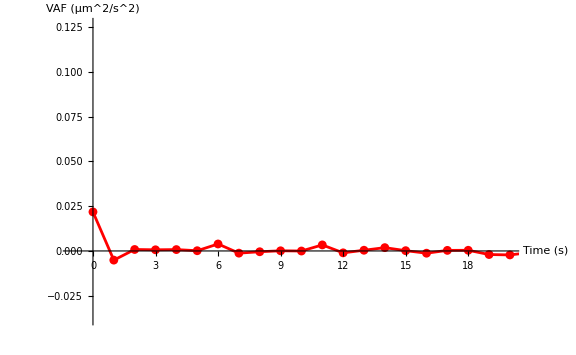

```mathematica
(****** Plot the average VAF *******)
If[Length[TrajInfoDirected]>0,
VAFTabD=VAFTab[[DirectedList]];        (* VAF corresponding to directed trajectories *)
VAFTabTrueAvD=Table[{(n-1)*FrameTime,Mean[Table[Select[VAFTabD,Length[#]>=n&][[i,n,2]],{i,Length[Select[VAFTabD,Length[#]>=n&]]}]]},{n,1,nframes-3}];
VAFPlotAvD=ListPlot[VAFTabTrueAvD,Joined->True,Mesh->All,PlotRange->{{-1,20},{-MaxVAF/10,MaxVAF/3}},PlotStyle->{Red},AxesLabel->{"Time (s)","VAF (µm^2/s^2)"},ImageSize->Large];
Print[VAFPlotAvD];,
VAFPlotAvD={}];
FirstPointD=VAFTabTrueAvD[[1,2]];SecondPointD=VAFTabTrueAvD[[2,2]];
```

FindFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (5).

Result of the normal diffusion fit (black) and velocity - variable error:{Diff→0.0034924,Vel→0.020554,Err→0.081269}

Result of the anomalous diffusion fit (red) :{Diff→0.0033082,al→1.14,Err→0.061078}

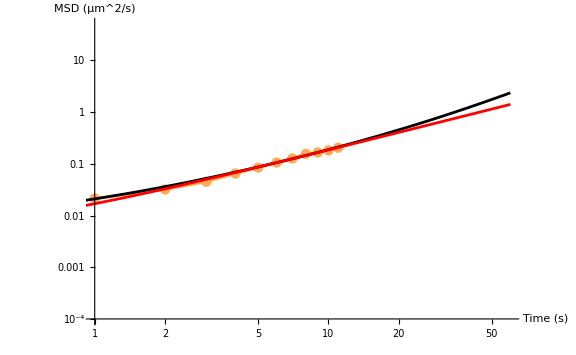

```mathematica
(*  Calculation and fit of the average MSD  *)
If[Length[TrajInfoDirected]>0,
MSDTabD=MSDTab[[DirectedList]];        (* MSD corresponding to immobile trajectories *)
MM=Max[Table[Length[MSDTabD[[i]]],{i,Length[MSDTabD]}]];      (* Length of the longer immobile trajectories *)
MSDTabAvTrue=Table[{(n-1)*FrameTime,Mean[Table[Select[MSDTabD,Length[#]>=n&][[i,n,2]],{i,Length[Select[MSDTabD,Length[#]>=n&]]}]]*10^12},{n,MM}];  (* Average of all the curves *)
MSDTabAvShortTrueD=Drop[Take[MSDTabAvTrue,nPMSD],1];
MSDPlotAvD=ListLogLogPlot[MSDTabAvShortTrueD,Joined->True,Mesh->All,PlotRange->{{1,60},{1*10^(-4),5*10^(1)}},PlotStyle->{Thick && Large,color3},AxesLabel->{"Time (s)","MSD (µm^2/s)"},ImageSize->Large];
LinePlot=ListLogLogPlot[{LineBrownian,LineDirected},Joined->True,PlotStyle->Dashed];
(* Model including a fraction p of particles undergoing directed motion *)
FitfunctionD[Diff_,p_,Vel_,Err_,t_]:=4*Abs[Diff]*t+p*Vel^2*t^2+Err^2;
(* Model including anomalous/caged diffusion *)
Fitfunction2D[Diff_,al_,Err_,t_]:=4*Diff*t^al+Err^2;
bestfit=FindFit[MSDTabAvShortTrueD,{FitfunctionD[Diff,1,Vel,Err,tt],Diff>0,Vel>0,Err>0},{{Diff,D2},{Vel,Veloce*10^(-6)},{Err,(Precisely*10^(-3))*10}},tt,WorkingPrecision->5,MaxIterations->1000];
FitPlotD=LogLogPlot[FitfunctionD[Diff,1,Vel,Err,tt]/.bestfit,{tt,0.1,60},PlotStyle->Black];
bestfit2=FindFit[MSDTabAvShortTrueD,Fitfunction2D[Diff,al,Err,tt],{{Diff,D1},{al,0.6},{Err,(Precisely*10^(-3))}},tt,WorkingPrecision->5,MaxIterations->1000];
FitPlot2D=LogLogPlot[Fitfunction2D[Diff,al,Err,tt]/.bestfit2,{tt,0.1,60},PlotStyle->Red];
Print["Result of the normal diffusion fit (black) and velocity - variable error:", bestfit];
Print["Result of the anomalous diffusion fit (red) :", bestfit2];
Show[MSDPlotAvD,FitPlotD,FitPlot2D]
,MSDPlotAvD={}
]
If[Output,OutputFile7={{"Directed trajectories",Length[TrajInfoDirected]},{"Cage size/localization precision (µm)",Err/.bestfit},{"Anomalous exponent",al/.bestfit2},{"Diffusion coefficient of directed particles (µm^2/s)",Diff/.bestfit},{"Speed of directed particles (µm/s)",Vel/.bestfit},{"VAF Directed (t=0)",FirstPointD},{"VAF Directed (t=1 frame)",SecondPointD}}];
```

```mathematica
Print["For individual trajectories, the median diffusion coefficient is: ", Median[Transpose[TrajInfoDirected][[13]]]*10^12,"µm^2/s"];
Print["And the median anomalous exponent is: ", Median[Transpose[TrajInfoDirected][[14]]],"."];
```

For individual trajectories, the median diffusion coefficient is: 0.00295303µm^2/s

And the median anomalous exponent is: 1.13618.

```mathematica
If[Output,Print[OutputFile7]];
```

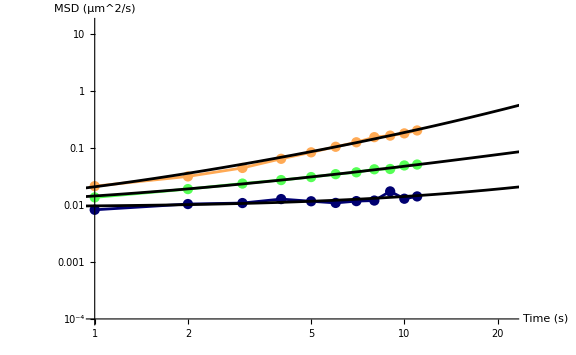

```mathematica
(* Show the average MSD of different categories of particles on the same plot: Green is immobile, Black is Brownian, Red is directed *)
Print[Show[MSDPlotAvI,FitPlotI,MSDPlotAvB,FitPlot2B,MSDPlotAvD,FitPlotD]]
```

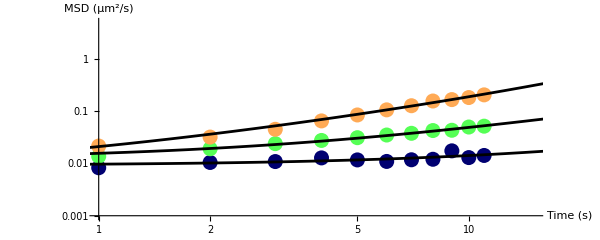

```mathematica
psize=0.018;
MSDPlotAvv=ListLogLogPlot[{MSDTabAvShortTrueI,MSDTabAvShortTrueB,MSDTabAvShortTrueD},PlotRange->{{1,15},{1*10^(-3),5}},AspectRatio->0.4,Joined->False,Mesh->All,ImageSize->600,PlotStyle->{{color1,PointSize->psize},{color2,PointSize->psize},{color3,PointSize->psize}},AxesLabel->{"Time (s)","MSD (µm^2/s)"},AxesStyle->Directive[Black, 18,Thickness[0.002]]];
Print[Show[MSDPlotAvv,FitPlotI,FitPlotB,FitPlotD]]
```

```mathematica
DataPs=ListPlot[{binneddistriberrF,binneddistriberrL},PlotRange->{{0,0.7},{0,20.5}},Joined->False,ImageSize->350,PlotStyle->{{Black,PointSize->0.015},{Darker[Green],PointSize->0.015}},Frame->True,FrameStyle->{{Directive[nfs,Black,Thickness[0.003]],Directive[nfs,White,Thickness[0.003]]},{Directive[nfs,Black,Thickness[0.003]],Directive[nfs,White,Thickness[0.003]]}},FrameLabel->{"δr (μm)","p(δr)"},PlotLegends->{"δt = " <>ToString[FrameTime*nfirst]<>" s","δt = " <>ToString[FrameTime*nlast]<>" s"}];
```

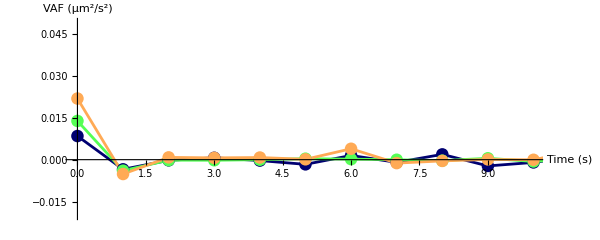

```mathematica
(* Show all the VAF on one plot: Green is immobile, Black is Brownian, Red is directed *)
psize=0.015;
VAFPlotAvI=ListPlot[{VAFTabTrueAvI,VAFTabTrueAvB,VAFTabTrueAvD},PlotRange->{{-0.05,10},{Vm,VM-0.001}},AspectRatio->0.4,Joined->True,Mesh->All,ImageSize->600,PlotStyle->{{color1,PointSize->psize},{color2,PointSize->psize},{color3,PointSize->psize}},AxesLabel->{"Time (s)","VAF (µm^2/s^2)"},AxesStyle->Directive[Black, 18,Thickness[0.002]]]
```

```mathematica
If[Output,OutputFile=Join[OutputFile1, OutputFile2,OutputFile3,OutputFile4,OutputFile5,OutputFile6,OutputFile7]];
If[Output,Export[NotebookDirectory[]<>DirName<>"/Output_"<>FileName<>"PaperFigure.xlsx",OutputFile]];
```

ANALYSIS OF AN INDIVIDUAL PARTICLE TRAJECTORY

```mathematica
(* Retained trajectories: *) SantaList
```

{3,4,6,7,11,13,14,15,19,20,24,25,26,28,30,31,32,38,40,43,46,47,49,51,54,58,59,61,62,65,66,70,71,73,74,75,78,79,81,86,87,88,89,92,95,96,97,100,102,107,108,115,117,118,119,120,122,126,130,133,134,141,144,148,150,156,158,160,161,163,167,172,177,178,180,187,189,194,195,196,197,200,206,210,211,221,224,226,227,228}

```mathematica
(* Immobile Trajectories: *) Transpose[TrajInfoImmobile][[1]]
```

{13,58,73,107,118,119,126,134,195,210,221,226,228}

```mathematica
(* Brownian Trajectories: *)Transpose[TrajInfoBrownian][[1]]
```

{4,6,7,11,14,19,20,24,25,26,28,30,31,32,38,49,51,59,61,65,66,70,71,74,78,79,87,89,95,96,97,100,102,108,115,117,120,122,130,133,141,144,148,150,156,158,161,163,172,177,178,180,187,194,196,197,200,206,211,224}

```mathematica
(* Directed Trajectories: *)Transpose[TrajInfoDirected][[1]]
```

{3,15,40,43,46,47,54,62,75,81,86,88,92,160,167,189,227}

Position of trajectory in the clean segmented file: 1

Number of times the particle has been detected: 59

Number of 1-frame step: 58

Average 1-step displacement: 0.0949185 μm

Minimum 1-step displacement: 0.000766706 μm

Maximum 1-step displacement: 0.616176 μm

Fraction of immobile moves: 46.5517 %

Fraction of diffusing moves: 50. %

Fraction of active moves: 3.44828 %

Diffusion coefficient calculated from MSD: 0.00576549 μm^2/s

Anomalous exponent calculated from MSD: 1.20484

Total displacement: 0.873101 μm/frame

Second point of the VAF: 0.00686568

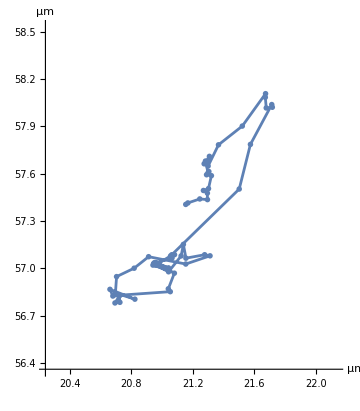

```mathematica
ni=Transpose[TrajInfoDirected][[1,1]];          (* Index of the trajectory, here chosen as the first directed trajectory, but instead ni can be set to any desired trajctory index *)
nn=Position[SantaList,ni][[1,1]];    (* Index of the trajectory in the clean segmented file *)
xmini=Min[Transpose[SegmentedFileClean[[nn]]][[1]]];
xmaxi=Max[Transpose[SegmentedFileClean[[nn]]][[1]]];ymini=Min[Transpose[SegmentedFileClean[[nn]]][[2]]];
ymaxi=Max[Transpose[SegmentedFileClean[[nn]]][[2]]];
Print["Position of trajectory in the clean segmented file: ",nn];
Print["Number of times the particle has been detected: ",TrajInfo[[nn,2]]];
Print["Number of 1-frame step: ",TrajInfo[[nn,6]]];
Print["Average 1-step displacement: ",TrajInfo[[nn,3]]*psm," μm"];
Print["Minimum 1-step displacement: ",TrajInfo[[nn,4]]*psm," μm"];
Print["Maximum 1-step displacement: ",TrajInfo[[nn,5]]*psm," μm"];
Print["Fraction of immobile moves: ",TrajInfo[[nn,10]]*100," %"];
Print["Fraction of diffusing moves: ",TrajInfo[[nn,11]]*100," %"];
Print["Fraction of active moves: ",TrajInfo[[nn,12]]*100," %"];
Print["Diffusion coefficient calculated from MSD: ",TrajInfo[[nn,13]]*10^12," μm^2/s"];
Print["Anomalous exponent calculated from MSD: ",TrajInfo[[nn,14]]];
Print["Total displacement: ",TrajInfo[[nn,15]]," μm/frame"];
Print["Second point of the VAF: ",TrajInfo[[nn,16]]," "];
ListPlot[SegmentedFileClean[[nn]]*psm,PlotRange->{{(xmini-2)*psm,(xmaxi+2)*psm},{(ymini-2)*psm,(ymaxi+2)*psm}},AspectRatio->(ymaxi-ymini+4)/(xmaxi-xmini+4),Joined->True,Mesh->All,ImageSize->Medium,AxesLabel->{"μm","μm"}]
```

{m→2.15728,s→0.0881033,f2→0.226049,s2→0.504472}

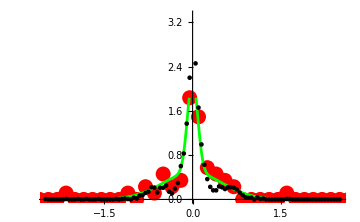

```mathematica
(********** Fit DisDis-x with a Gaussian ********)
Fitfunction[m_,s_,f2_,s2_,pix_]:=m*(1-f2)*ⅇ^(-pix^2/(2 s^2))+f2*m*ⅇ^(-pix^2/(2 s2^2)) ; 
BinSize=0.15;
(* Plot distribution *)
ListDisshort=Transpose[PlotDis[[nn]]][[2]];
MM=Max[ListDisshort];mm=Min[ListDisshort];MMmm=Round[Max[MM,-mm],BinSize];
Bins=Table[i,{i,-MMmm-2,MMmm+2,BinSize}];
BinCs=BinCounts[ListDisshort,{-MMmm-2-BinSize/2,MMmm+2+BinSize/2,BinSize}];
binneddistrib0=Transpose[{Bins,BinCs}];
binneddistrib=Table[{binneddistrib0[[i,1]],binneddistrib0[[i,2]]/Length[ListDisshort]/BinSize},{i,Length[binneddistrib0]}];
DataPx1=ListPlot[binneddistrib,PlotRange->{{-2.5,2.5},{0,Max[Transpose[binneddistrib][[2]]]+1.5}},PlotStyle->{Red,PointSize[0.03]},ImageSize->Medium];
(* 2-component fit *)
bestfit2x1=FindFit[binneddistrib,{Fitfunction[m,s,f2,s2,pix]},{{m,Max[Transpose[binneddistrib][[2]]]},{s,0.2},{f2,0.2},{s2,0.6}},pix];
FitP2x1=Plot[Fitfunction[m,s,f2,s2,pix]/.bestfit2x1,{pix,-2,2},PlotRange->{0,Max[Transpose[binneddistrib][[2]]]},PlotStyle->Green]; 
Print[bestfit2x1];
Show[DataPx1,FitP2x1,DataPx]
```

{m→2.4969,s→0.0767058,f2→0.470011,s2→0.577276}

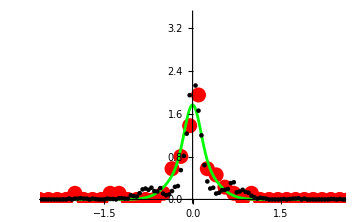

```mathematica
(********** Fit DisDis-y with a Gaussian ********)
Fitfunction[m_,s_,f2_,s2_,pix_]:=m*(1-f2)*ⅇ^(-pix^2/(2 s^2))+f2*m*ⅇ^(-pix^2/(2 s2^2)) ; BinSize=0.15;
(* Plot distribution *)
ListDisshort=Transpose[PlotDis[[nn]]][[3]];
MM=Max[ListDisshort];mm=Min[ListDisshort];MMmm=Round[Max[MM,-mm],BinSize];
Bins=Table[i,{i,-MMmm-2,MMmm+2,BinSize}];
BinCs=BinCounts[ListDisshort,{-MMmm-2-BinSize/2,MMmm+2+BinSize/2,BinSize}];
binneddistrib0=Transpose[{Bins,BinCs}];
binneddistrib=Table[{binneddistrib0[[i,1]],binneddistrib0[[i,2]]/Length[ListDisshort]/BinSize},{i,Length[binneddistrib0]}];
DataPy1=ListPlot[binneddistrib,PlotRange->{{-2.5,2.5},{0,Max[Transpose[binneddistrib][[2]]]+1.5}},PlotStyle->{Red,PointSize[0.03]},ImageSize->Medium];
(* 2-component fit *)
bestfit2y1=FindFit[binneddistrib,{Fitfunction[m,s,f2,s2,pix]},{{m,Max[Transpose[binneddistrib][[2]]]},{s,02},{f2,0.2},{s2,0.6}},pix];
FitP2y1=Plot[Fitfunction[m,s,f2,s2,pix]/.bestfit2y1,{pix,-2,2},PlotRange->{0,Max[Transpose[binneddistrib][[2]]]},PlotStyle->Green]; 
Print[bestfit2y];
Show[DataPy1,FitP2y1,DataPy]
```

General::munfl: Exp[-3433.43] is too small to represent as a normalized machine number; precision may be lost.

{m→0.00354877,s→-0.0241342,f2→0.952,s2→-0.0764547}

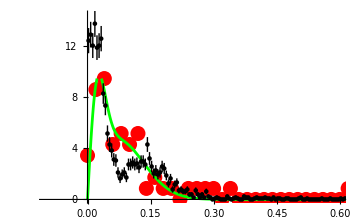

```mathematica
(********** Fit radial DisDis with Rayleigh expression ********)
BinSize=0.02;
Fitfunction2Single[m_,s_,f2_,s2_,pix_]:=(m/s^2 )*(1-f2)*pix*ⅇ^(-pix^2/(2 s^2))/s^2+f2*(m/s2^2 )*pix*ⅇ^(-pix^2/(2 s2^2))/s2^2 ; 
(* Plot distribution *)
ListDisshort=Transpose[PlotDis[[nn]]][[1]]*psm;
MM=Max[ListDisshort];mm=Min[ListDisshort];MMmm=Round[Max[MM,-mm],BinSize];
Bins=Table[i,{i,0,MMmm+2,BinSize}];
BinCs=BinCounts[ListDisshort,{-BinSize/2,MMmm+2+BinSize/2,BinSize}];
binneddistrib0=Transpose[{Bins,BinCs}];
binneddistrib=Table[{binneddistrib0[[i,1]],binneddistrib0[[i,2]]/Length[ListDisshort]/BinSize},{i,Length[binneddistrib0]}];
DataPxy1=ListPlot[binneddistrib,PlotRange->{{-0.1,0.6},{0,Max[Transpose[binneddistrib][[2]]]+5}},PlotStyle->{Red,PointSize[0.03]},ImageSize->Medium];
(* 2-component fit *)
bestfit2r1=FindFit[binneddistrib,{Fitfunction2Single[m,s,f2,s2,pix]},{{m,Max[Transpose[binneddistrib][[2]]]},{s,02},{f2,0.2},{s2,0.6}},pix];
FitP2r1=Plot[Fitfunction2Single[m,s,f2,s2,pix]/.bestfit2r1,{pix,-2,2},PlotRange->{0,Max[Transpose[binneddistrib][[2]]]},PlotStyle->Green]; 
Print[bestfit2r1];
Show[DataPxy1,FitP2r1,DataP]
```

{betat→-13.6371,al→1.20484}

Diffusion coefficient: 5.76549×10^-15 m^2/s

Anomalous exponent: 1.20484

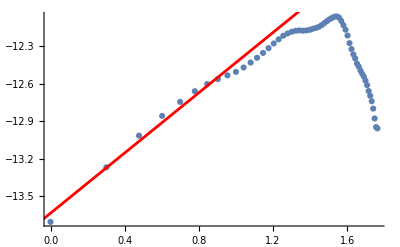

```mathematica
(* Linear fit of the log-log MSD *)
DataList=N[Log[10,Drop[MSDTab[[nn]],1]]];
DataPlot=ListPlot[DataList,PlotRange->Full];
DataListShort=Take[DataList,10];    (* Keep only the first... points for the fit *)
Fitfunction[betat_,al_,tt_]:=betat+al*tt;
bestfit=FindFit[DataListShort,Fitfunction[betat,al,tt],{{betat,-10},{al,1}},tt];
FitPlot=Plot[Fitfunction[betat,al,tt]/.bestfit,{tt,-50,50},PlotStyle->Red];
DD=10^(betat/.bestfit)/4; (* Diffusion coefficient *)
AA = al/.bestfit; (* Anomalous exponent *)
Print[bestfit];
Print["Diffusion coefficient: ",DD," m^2/s"];
Print["Anomalous exponent: ",AA];
Show[DataPlot,FitPlot]
```

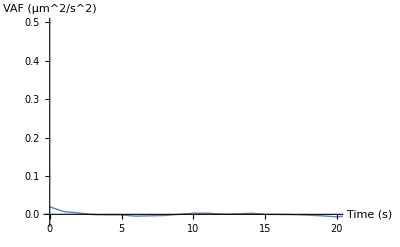

```mathematica
(* Plot the VAF of a particular trajectory *)
ListPlot[VAFTab[[nn]],Joined->True,PlotRange->{{0,20},{-0.02,0.5}},PlotStyle->Thick,AxesLabel->{"Time (s)","VAF (µm^2/s^2)"}]
```

SUMMARY OF TRAJECTORY CHARACTERISTICS

```mathematica
(* TrajInfo: (1) Trajectory #, (2) Trajectory length (frame), (3) Average, (4) min, and (5) max 1-step displacement (pixel), (6) number of 1-frame intervals, (7) number of immobile moves, (8) diffusing moves and (9) active moves, (10) fraction of immobile moves, (11) diffusing moves and (12) active moves, (13) diffusion coefficient, (14) anomalous exponent, (15)total displacement (micron), (16) Value of the average VAF at t = FrameTime (17) Max individual value of the VAF at t = FrameTime   *)
```

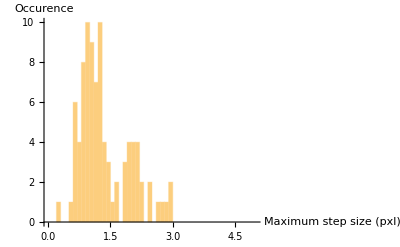

```mathematica
(* Distribution of maximum step size (in pixel)*)
Print[Histogram[Transpose[TrajInfo][[5]],{0,displ,0.1},AxesLabel->{"Maximum step size (pxl)", "Occurence"}]];
```

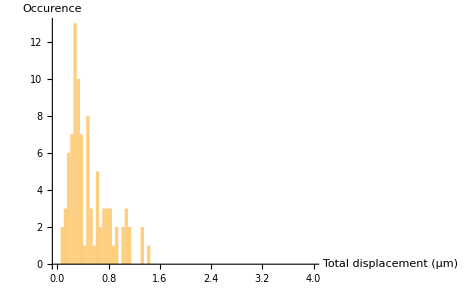

```mathematica
(* Distribution of total displacement  (in micron)*)
Print[Histogram[Transpose[TrajInfo][[15]],{0,4,0.05},AxesLabel->{"Total displacement (µm)", "Occurence"}]];
```

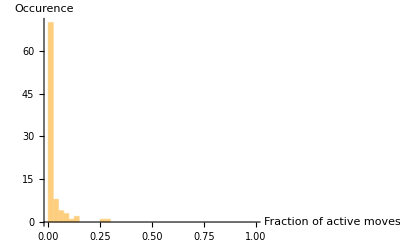

```mathematica
(* Fraction of active moves *)
Print[Histogram[Transpose[TrajInfo][[12]],{0,1,0.025},AxesLabel->{"Fraction of active moves", "Occurence"}]];
```

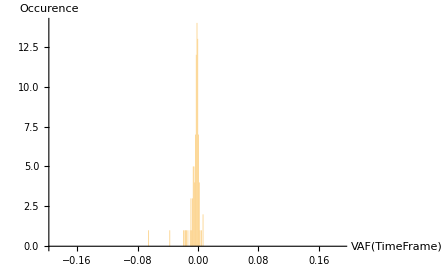

```mathematica
(* Average value of the VAF at t = FrameTime *)
Print[Histogram[Transpose[TrajInfo][[16]],{-MaxVAF/2,MaxVAF/2,0.001},AxesLabel->{"VAF(TimeFrame)", "Occurence"}]];
```

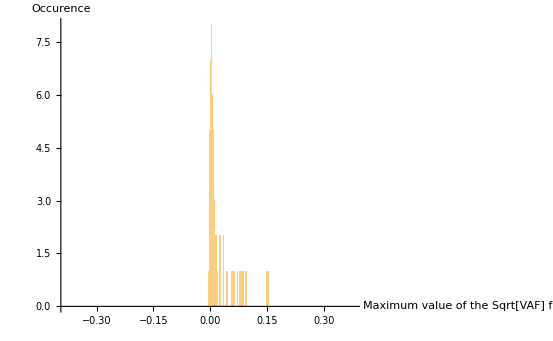

```mathematica
(* Maximum value of the Sqrt[VAF] at t=FrameTime *)
Print[Histogram[Transpose[TrajInfo][[17]],{-MaxVAF,MaxVAF,0.001},AxesLabel->{"Maximum value of the Sqrt[VAF] for t = TimeFrame", "Occurence"}]];
```

```mathematica
(* Compare the average value of VAF(1) and the max value of VAF(1) *)
n1=16;n2=17;
ListLogPlot[{Transpose[{Transpose[TrajInfo][[n1]],Transpose[TrajInfo][[n2]]}],Transpose[{Transpose[TrajInfoDirected][[n1]],Transpose[TrajInfoDirected][[n2]]}]},PlotRange->All];
```

Part::partw: Part 16 of Transpose[TrajInfoDirected] does not exist.

Part::partw: Part 17 of Transpose[TrajInfoDirected] does not exist.

```mathematica
(* Compare the fraction of active moves and the max value of VAF(1) *)
n1=12;n2=17;
ListLogPlot[{Transpose[{Transpose[TrajInfo][[n1]],Transpose[TrajInfo][[n2]]}],Transpose[{Transpose[TrajInfoDirected][[n1]],Transpose[TrajInfoDirected][[n2]]}]},PlotRange->All];
```

Part::partw: Part 12 of Transpose[TrajInfoDirected] does not exist.

Part::partw: Part 17 of Transpose[TrajInfoDirected] does not exist.

```mathematica
(* Compare the total displacement (/number of frames) and the max value of VAF(1) *)
n1=15;n2=17;
ListLogLogPlot[{Transpose[{Transpose[TrajInfo][[n1]],Transpose[TrajInfo][[n2]]}],Transpose[{Transpose[TrajInfoDirected][[n1]],Transpose[TrajInfoDirected][[n2]]}]},PlotRange->All];
```

Part::partw: Part 15 of Transpose[TrajInfoDirected] does not exist.

Part::partw: Part 17 of Transpose[TrajInfoDirected] does not exist.

```mathematica
(* Compare the maximum displacement and the max value of VAF(1) *)
n1=5;n2=17;
ListLogLogPlot[{Transpose[{Transpose[TrajInfo][[n1]],Transpose[TrajInfo][[n2]]}],Transpose[{Transpose[TrajInfoDirected][[n1]],Transpose[TrajInfoDirected][[n2]]}]},PlotRange->All];
```

Part::partw: Part 5 of Transpose[TrajInfoDirected] does not exist.

Part::partw: Part 17 of Transpose[TrajInfoDirected] does not exist.

```mathematica
(* Compare the anomalous exponent and the max value of VAF(1) *)
n1=14;n2=17;
ListLogPlot[{Transpose[{Transpose[TrajInfo][[n1]],Transpose[TrajInfo][[n2]]}],Transpose[{Transpose[TrajInfoDirected][[n1]],Transpose[TrajInfoDirected][[n2]]}]},PlotRange->All];
```

Part::partw: Part 14 of Transpose[TrajInfoDirected] does not exist.